```mathematica
NMConstantsToParameters[ListParamsIn_]:=Module[{EE,KK,SMASS,RHO,ASS,LASS,Crdr,CrdJ},
{EE,KK,SMASS,RHO,ASS,LASS,Crdr,CrdJ}=ListParamsIn;
c13=1.0/3.0;
c23=2.0/3.0;
VMASS=1.25000101440918243;
kfconst=(1.50*Pi^2)^(1.0/3.0);
CK=3.0/5.0*kfconst^2;
hbzero=20.73553;
mpi=138.03/197.3;
tauc=CK*RHO^c23;
u=(kfconst/mpi)*RHO^c13;
rho2=RHO^2;
Crho={0.0,0.0};
Cdrho={0.0,0.0};
Ctau={0.0,0.0};
INsigma=((1.0/3.0)*(-KK+tauc*hbzero*(-3.0+4.0*SMASS)-9.0*EE))/(tauc*hbzero*(-3.0+2.0*SMASS)+3.0*EE);

Crho[[1]]=(c13*(tauc*hbzero*(-3.0+(2.0-3.0*INsigma)*SMASS)+3.0*(1.0+INsigma)*EE))/(INsigma*RHO);

Cdrho[[1]]=(c13*RHO^(-1.0-INsigma)*(tauc*hbzero*(3.0-2.0*SMASS)-3.0*EE))/INsigma;
Ctau[[1]]=(hbzero*(SMASS-1.0))/RHO;
Crho[[2]]=(27.0*ASS*(1.0+INsigma)-9.0*LASS+5.0*tauc*hbzero*(5.0-6.0*VMASS+3.0*INsigma*(-4.0+3.0*VMASS))+RHO*(40.0*tauc*Ctau[[1]]-60.0*tauc*INsigma*Ctau[[1]]))/(27.0*INsigma*RHO);

Cdrho[[2]]=-(RHO^(-1.0-INsigma)*(27.0*ASS-9.0*LASS+5.0*tauc*hbzero*(5.0-6.0*VMASS)+40.0*tauc*RHO*Ctau[[1]]))/(27.0*INsigma);
Ctau[[2]]=(hbzero-hbzero*VMASS+RHO*Ctau[[1]])/RHO;

INt0=(8.0/3)*Crho[[1]];
INt1=4.0/3.0*(Ctau[[1]]-4.0*Crdr[[1]]);
INt2=4.0/3.0*(3.0*Ctau[[1]]-6.0*Ctau[[2]]+4.0*Crdr[[1]]-8.0*Crdr[[2]]);
INt3=16.0*Cdrho[[1]];
INx0=-0.50*(3.0*Crho[[2]]/Crho[[1]]+1.0);
INx1=2.0*(-Ctau[[1]]-3.0*Ctau[[2]]+4.0*Crdr[[1]]+12.0*Crdr[[2]])/INt1/3.0;

INx2=-2.0*(3.0*Ctau[[1]]-15.0*Ctau[[2]]+4.0*Crdr[[1]]-20.0*Crdr[[2]])/INt2/3.0;
INx3=-0.50*(3.0*Cdrho[[2]]/Cdrho[[1]]+1.0);
INt4=(CrdJ[[2]]-CrdJ[[1]])/2.0;
INt4p=-CrdJ[[2]]*4.0;






(*(*[t0,t1,t2,t3,x0,x1,x2,x3,w0,sig]*)
{INt0,INt1,INt2,INt3,INx0,INx1,INx2,INx3,INt4p,INsigma}*)


(*[t0,x0,t1,x1,t2,x2,t3,x3,w0,sig]*)
{INt0,INx0,INt1,INx1,INt2,INx2,INt3,INx3,INt4p,INsigma}

]
```

```mathematica
Params0=NMConstantsToParameters[{-15.8,220.0,0.992423332283364,0.158706769332587,28.986789057772100,40.004790480413600,{-45.1351310222373,-145.382167908057},{-74.0263331764599,-35.6582611147917}}]
```

{-2078.33,0.0536509,239.401,-5.07706,1575.29,-1.36649,14263.6,-0.162747,142.633,0.270018}

```mathematica
NMConstantsToParameters[{-15.8,220.0,0.992423332283364,0.158706769332587,28.986789057772100,40.004790480413600,{-45.1351310222373,-145.382167908057},{-74.0263331764599,-35.6582611147917}}]
```

{-2078.33,0.0536509,239.401,-5.07706,1575.29,-1.36649,14263.6,-0.162747,142.633,0.270018}

```mathematica
(*Important: We should have a check/flag routine to make sure that when the solutions converge to something, it is something with the necesary properties: it goes to zero for large rs. If it does not, some warning should be raised*)

(*Check if everything is ok with the factors of 4Pi that Kyle has but Jorge does not*)
hbarc=197.33;
e0=Sqrt[1.4399784];
(*e0=0;*)

MassNucleon=939;
(*hbar22m=hbarc^2/(2*MassNucleon);*)
hbar22m=20.73553;                             
dx=0.01;   (*Step size for the finite element method*)
Xmin=dx;                                    (* Lower limit range for the function *)
Xmax=15-dx;                                     (* Upper limit range for the function *)
x=Range[Xmin,Xmax,dx]; (*Initialize the abcissa. IMPORTANT: It starts at dx, not at zero, such that the value of any function at zero is never a variable for the finite element equations. By building the derivative matrices with this in mind, we don't have an issue with things blowing up at zero since in many places we divde by r or r^2.*)

len=Length[x];     (*Initialize the lengeth of solution vector*)
```

```mathematica
(*******************************)
```

```mathematica
(*Centered Derivatives*)
```

```mathematica
(*Double derivative matrix*)
D2MatEven=SparseArray[{Band[{1,1}]->-30,Band[{2,1}]->16,Band[{1,2}]->16,Band[{1,3}]->-1,Band[{3,1}]->-1},{len,len}]/(12*dx^2);
```

```mathematica
D2MatOdd=SparseArray[{Band[{1,1}]->-30,Band[{2,1}]->16,Band[{1,2}]->16,Band[{1,3}]->-1,Band[{3,1}]->-1},{len,len}]/(12*dx^2);
```

```mathematica
D2MatEven[[1]][[1]]=-31/(12*dx^2);
```

```mathematica
D2MatOdd[[1]][[1]]=-29/(12*dx^2);
```

```mathematica
(*Single derivative matrix*)
D1MatEven=SparseArray[{Band[{2,1}]->-8,Band[{1,2}]->8,Band[{1,3}]->-1,Band[{3,1}]->1},{len,len}]/(12*dx);
```

```mathematica
D1MatOdd=SparseArray[{Band[{2,1}]->-8,Band[{1,2}]->8,Band[{1,3}]->-1,Band[{3,1}]->1},{len,len}]/(12*dx);
```

```mathematica
D1MatOdd[[1]][[1]]=-1/(12*dx);
```

```mathematica
D1MatEven[[1]][[1]]=1/(12*dx);
```

```mathematica
D2MatFieldsEven=SparseArray[{Band[{1,1}]->-30,Band[{2,1}]->16,Band[{1,2}]->16,Band[{1,3}]->-1,Band[{3,1}]->-1},{len,len}]/(12*dx^2);
D2MatFieldsEven[[1]][[1]]=-15/(12*dx^2);
```

```mathematica
D2MatFieldsEven[[2]][[1]]=15/(12*dx^2);
```

```mathematica
D2MatFieldsEven*(12*dx^2)
```

SparseArray[…]

```mathematica
D1MatFieldsEven=SparseArray[{Band[{2,1}]->-8,Band[{1,2}]->8,Band[{1,3}]->-1,Band[{3,1}]->1},{len,len}]/(12*dx);
```

```mathematica
D1MatFieldsEven[[1]][[1]]=-7/(12*dx);
D1MatFieldsEven[[2]][[1]]=-7/(12*dx);
```

```mathematica
(*******************************)
```

## Importing data from files and some by hand that defines the nucleus we have

```mathematica
(*Function that takes a list evaluated in a grid, and transforms it into a list in another grid*)
InterpolatorFunction[list_,xold_,xnew_]:=Module[{inter},
inter=Interpolation[Transpose[{xold,list}]];
Table[inter[xnew[[i]]],{i,1,Length[xnew]}]

]
```

```mathematica
NucleusName="48Ca"
```

48Ca

```mathematica
A=48;
```

```mathematica
(*XJorge=Range[0,20,0.05];*)
```

```mathematica
SetDirectory[NotebookDirectory[]] (*So we can import files directly from this directory*)
```

```mathematica
(*This should be technically XKyle, but I don't want to sit down and change the name everywhere*)
```

```mathematica
XJorge=Transpose[Import["Ca48Sky/fort.21"]][[1]][[2;;-2]];
```

```mathematica
(*We are using the notation from the RMF code, so in here "g" is the only wave function associated with each nucleon, while in the other code we had gs and fs for the Dirac spinor.*)
```

```mathematica
gneutrons01=Transpose[Import["Ca48Sky/fort.21"]][[2]][[2;;-2]];
gneutrons02=Transpose[Import["Ca48Sky/fort.22"]][[2]][[2;;-2]];
gneutrons03=Transpose[Import["Ca48Sky/fort.23"]][[2]][[2;;-2]];
gneutrons04=Transpose[Import["Ca48Sky/fort.24"]][[2]][[2;;-2]];
gneutrons05=Transpose[Import["Ca48Sky/fort.25"]][[2]][[2;;-2]];
gneutrons06=Transpose[Import["Ca48Sky/fort.26"]][[2]][[2;;-2]];
gneutrons07=Transpose[Import["Ca48Sky/fort.27"]][[2]][[2;;-2]];
```

```mathematica
gprotons01=Transpose[Import["Ca48Sky/fort.41"]][[2]][[2;;-2]];
gprotons02=Transpose[Import["Ca48Sky/fort.42"]][[2]][[2;;-2]];
gprotons03=Transpose[Import["Ca48Sky/fort.43"]][[2]][[2;;-2]];
gprotons04=Transpose[Import["Ca48Sky/fort.44"]][[2]][[2;;-2]];
gprotons05=Transpose[Import["Ca48Sky/fort.45"]][[2]][[2;;-2]];
gprotons06=Transpose[Import["Ca48Sky/fort.46"]][[2]][[2;;-2]];
```

```mathematica
gneutrons0={gneutrons01,gneutrons02,gneutrons03,gneutrons04,gneutrons05,gneutrons06,gneutrons07};

gprotons0={gprotons01,gprotons02,gprotons03,gprotons04,gprotons05,gprotons06};
```

```mathematica
gneutrons={};

gprotons={};
```

```mathematica
For[k=1,k<=Length[gneutrons0],k++,
AppendTo[gneutrons,InterpolatorFunction[gneutrons0[[k]],XJorge,x]];

];
```

InterpolatingFunction::dmval: Input value {0.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.02} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.03} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
For[k=1,k<=Length[gprotons0],k++,

AppendTo[gprotons,InterpolatorFunction[gprotons0[[k]],XJorge,x]];

];
```

InterpolatingFunction::dmval: Input value {0.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.02} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.03} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

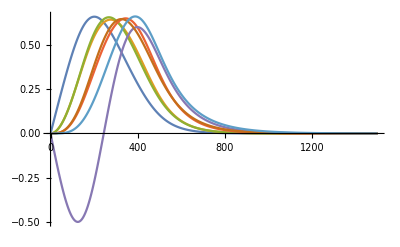

```mathematica
ListPlot[gneutrons,Joined->True]
```

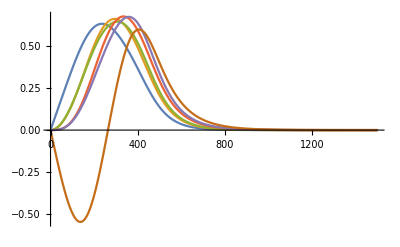

```mathematica
ListPlot[gprotons,Joined->True]
```

```mathematica
(*In here we specify the Kappa values for the different levels of protons and neutrons. For s it is either +1 if it is -1/2 or +2 if it is +1/2*)
```

```mathematica
nL={0,1,1,2,0,2,3};
ns={1,2,1,2,1,1,2};
```

```mathematica
pL={0,1,1,2,2,0};
```

```mathematica
ps={1,1,2,1,2,1};

nEn={36.719,27.375,25.75,17.71,15.53,14.38,8.09};
pEn={37.75,29.91,29.11,19.76,19.21,16.05};
```

```mathematica
JTransformerFromLS[lList_,slist_]:=Table[Abs[lList[[i]]+(slist[[i]]-1.5)],{i,1,Length[lList]}];
```

```mathematica
nJ=JTransformerFromLS[nL,ns];
pJ=JTransformerFromLS[pL,ps];
```

```mathematica
ChiTransformer[ll_,jj_]:=If[ll-1/2==jj,ll,-(ll+1)]
```

```mathematica
ChiTransformerList[llList_,jjList_]:=Table[ChiTransformer[llList[[ii]],jjList[[ii]]],{ii,1,Length[llList]}]
```

```mathematica
nChi=ChiTransformerList[nL,nJ];
```

```mathematica
pChi=ChiTransformerList[pL,pJ];
```

```mathematica
NeutronLevelsKappa=nChi;
ProtonLevelsKappa=pChi;
```

```mathematica
LJChecker[ChiValueList_]:=Module[{ListValues},
ListValues={};

For[IJIJI=1,IJIJI<=Length[ChiValueList],IJIJI++,
j=(Abs[ChiValueList[[IJIJI]]]-1/2);
If[ChiValueList[[IJIJI]]>= 0,
l=ChiValueList[[IJIJI]],
l=-1-ChiValueList[[IJIJI]]
];
AppendTo[ListValues,{l,j}];
];
ListValues
]
```

```mathematica
NeutronLevelsEnergy=nEn;
ProtonLevelsEnergy=pEn;
```

```mathematica
NeutronLevels=Length[NeutronLevelsKappa];
ProtonLevels=Length[ProtonLevelsKappa];
```

```mathematica
(*The following are the master lists, each element a different level the g wave function*)
```

```mathematica
ListOfWN=gneutrons;
```

```mathematica
ListOfWP=gprotons;
```

```mathematica
(*Energies in MeV for protons and neutrons*)
```

```mathematica
ListOfEnergies={
ProtonLevelsEnergy,
NeutronLevelsEnergy
};
```

```mathematica
(*Chis (Kappas) for protons and neutrons*)
```

```mathematica
ListOfChis={
ProtonLevelsKappa,
NeutronLevelsKappa

};
```

```mathematica
ListOfChis
```

{{-1,1,-2,2,-3,-1},{-1,-2,1,-3,-1,2,-4}}

```mathematica
LJChecker[ListOfChis[[2]]]
```

{{0,1/2},{1,3/2},{1,1/2},{2,5/2},{0,1/2},{2,3/2},{3,7/2}}

## Writing the non-linear equations for the fields

```mathematica
(*SUPER IMPORTANT, DONT FORGET TO ACCOUNT FOR THE RADIUS SCALE R WHEN TAKING DERIVATIVES AND EVERYTHING ELSE*)
```

```mathematica
(*Annoying conversion of units because DFT people don't seem to be able to agree to write their equations in a consistent way with a single group of variables, so now we have to translate stuff at least two times. Who knows, maybe they will decide to re-write their equations in terms of the zoodiac signs and we will have to change them every time that Mars goes retrograde.*)
```

```mathematica
cmcorr=1.0-(1.0/A);
a0r0=3.0/8.0*t0;
a1r1=-1.0/4.0*t0*(1.0/2.0+x0);
a0s0=-1.0/4.0*t0*(1.0/2.0-x0);
a1s1=-1.0/8.0*t0;

a0tau0=3.0/16.0*t1+1.0/4.0*t2*(5.0/4.0+x2);
a1tau1=-1.0/8.0*t1*(1.0/2.0+x1)+1.0/8.0*t2*(1.0/2.0+x2);

a0t0=-1.0/8.0*t1*(1.0/2.0-x1)+1.0/8.0*t2*(1.0/2.0+x2);
a1t1=1.0/16.0*(t2-t1);

a0r0p=-9.0/64.0*t1+1.0/16.0*t2*(5.0/4.0+x2);
a1r1p=3.0/32.0*t1*(1.0/2.0+x1)+1.0/32.0*t2*(1.0/2.0+x2);

a0s0p=3.0/32.0*t1*(1.0/2.0-x1)+1.0/32.0*t2*(1.0/2.0+x2);
a1s1p=3.0/64.0*t1+1.0/64.0*t2;

cddr0=t3/16.00;
cddr1=-1.0/24.0*t3*(1.0/2.0+x3);
cdds0=-1.0/24.0*t3*(1.0/2.0-x3);
cdds1=-1.0/48.0*t3;

cso0=-3.0/4.0*W;
cso1=-1.0/4.0*W;
```

```mathematica
Uc=2*(a0r0-a1r1)*rhotot+4*a1r1*rho+(a0tau0-a1tau1)*tautot+2*a1tau1*tau+2*(a0r0p-a1r1p)*(Dd2.rhotot+2*(Dd1.rhotot)/r)+4*a1r1p*(Dd2.rho+2*(Dd1.rho)/r);
Ucso=(cso0-cso1)*(Ddd1.jsctot+2*jsctot/r)+2*cso1*(Ddd1.jsc+2*jsc/r);
Umr=hbar22m*cmcorr+(a0tau0-a1tau1)*rhotot+2*a1tau1*rho;
DUmr=(a0tau0-a1tau1)*Dd1.rhotot+2*a1tau1*Dd1.rho;
Udd=(2+sig)*(cddr0-cddr1)*rhotot^(sig+1)+2*sig*cddr1*(rhon^2+rhop^2)*rhotot^(sig-1.)+4*cddr1*rho*rhotot^sig;
Uso=-(cso0-cso1)*(Dd1.rhotot)/r-2*cso1*(Dd1.rho)/r-(a0t0-a1t1)*jsctot/r-2*a1t1*jsc/r;
```

```mathematica
Ucoul=4*Pi*e^2*AField-e^2*(3/Pi)^(1/3)*rhop^(1/3);
```

```mathematica
UcoulAffine=4*Pi*e^2*AField;
UcoulNONAffine=-e^2*(3/Pi)^(1/3)*rhop^(1/3);
```

```mathematica
e0
```

1.19999

```mathematica
e0^2
```

1.43998

```mathematica
eqnsN=Umr*D2.WF + DUmr*D1.WF+(-Uc-Ucso-Udd-Uso*(J*(J+1)-L*(L+1)-0.75)-DUmr/r-Umr*L*(L+1)/r^2)*WF-lambda*WF;
eqnsP=Umr*D2.WF + DUmr*D1.WF+(-Uc-Ucso-Udd-Uso*(J*(J+1)-L*(L+1)-0.75)-DUmr/r-Umr*L*(L+1)/r^2 -Ucoul)*WF-lambda*WF;
```

```mathematica
eqnsNRBAffine=Umr*D2.WF + DUmr*D1.WF+(-Uc-Ucso-Uso*(J*(J+1)-L*(L+1)-0.75)-DUmr/r-Umr*L*(L+1)/r^2)*WF-lambda*WF;
```

```mathematica
eqnsPRBAffine=Umr*D2.WF + DUmr*D1.WF+(-Uc-Ucso-Uso*(J*(J+1)-L*(L+1)-0.75)-DUmr/r-Umr*L*(L+1)/r^2 -UcoulAffine)*WF-lambda*WF;
```

```mathematica
eqnsNRBNONAffine=-Udd*WF;
eqnsPRBNONAffine=(-Udd-UcoulNONAffine)*WF;
```

```mathematica
(*eqnsNRB=Umr*D2.WF + DUmr*D1.WF+(-Uc-0*UddRB-Ucso-Uso*(J*(J+1)-L*(L+1)-0.75)-DUmr/r-Umr*L*(L+1)/r^2)*WF-lambda*WF;*)
```

```mathematica
(*eqnsPRB=Umr*D2.WF + DUmr*D1.WF+(-Uc-0*UddRB-Ucso-Uso*(J*(J+1)-L*(L+1)-0.75)-DUmr/r-Umr*L*(L+1)/r^2 -0*UcoulRB)*WF-lambda*WF;*)
```

## Helper functions to build densities and the photon field

```mathematica
(*Why in this Skyrme interaction we have a factor of 4Pi but we don't on the RMF one?*)
```

```mathematica
ABuilder[ρprot_]:=Module[{sum1,sum2,Ar},
sum1=Accumulate[x^2*ρprot]*dx;
sum2=Reverse[Accumulate[Reverse[x*ρprot]]]*dx;

Ar={};
For[ij=1,ij<=Length[x],ij++,
AppendTo[Ar,1/x[[ij]]*sum1[[ij]]+sum2[[ij]]]


];

Ar

]
```

```mathematica
DensitiesBuilder[ListOfWaveFuncs_,ChiValueList_]:=Module[{rhonIN,rhopIN,rhototIN,protfuncsIN,neutfuncsIN,taupIN,taunIN,jscpIN,jscnIN},
(*make sure the derivatives make sense *)
(*
ListOfWaveFuncs should be formated in the following way:

ListOfWaveFuncs= {Protons,   Neutrons  }
where Protons ={{chi1,  g_chi1}, {chi2,  g_chi2}, ....  } 
and similar for neutrons. Chi is the associated shorthand for the angular momentum

*)


(*
ListOfWaveFuncs should be formated in the following way:

ListOfWaveFuncs= {Protons,   Neutrons  }
where Protons ={g_chi1,  g_chi2, ....  } 
and similar for neutrons. 

*)

(*ChiValueList= {
{chiproton1,chiproton2,....}
,
{chineutron1,chineutron2,...}}
*)


rhopIN=ConstantArray[0,Length[x]];
rhonIN=ConstantArray[0,Length[x]];
taupIN=ConstantArray[0,Length[x]];
taunIN=ConstantArray[0,Length[x]];
jscpIN=ConstantArray[0,Length[x]];
jscnIN=ConstantArray[0,Length[x]];
rhototIN=ConstantArray[0,Length[x]];

protfuncsIN=ListOfWaveFuncs[[1]];
neutfuncsIN=ListOfWaveFuncs[[2]];


(*Proton loop*)
For[ij=1,ij<=Length[protfuncsIN],ij++,
g2=protfuncsIN[[ij]]^2;

rhopIN=rhopIN+g2*(2*(Abs[ChiValueList[[1]][[ij]]]-1/2)+1);

];
rhopIN=rhopIN/(4*Pi)*(1/x^2);

(*rhop[[1]]=rhop[[2]];*)
(****************************)


(*Neutron loop*)

For[ij=1,ij<=Length[neutfuncsIN],ij++,
g2=neutfuncsIN[[ij]]^2;

rhonIN=rhonIN+g2*(2*(Abs[ChiValueList[[2]][[ij]]]-1/2)+1);

];
rhonIN=rhonIN/(4*Pi)*(1/x^2);

(*rhon[[1]]=rhon[[2]];*)
(****************************)


(*Taun loop*)
For[ij=1,ij<=Length[neutfuncsIN],ij++,

wf=neutfuncsIN[[ij]];
If[ChiValueList[[2]][[ij]] >= 0,
l=ChiValueList[[2]][[ij]],
l=-1-ChiValueList[[2]][[ij]]
];


(*Important distinction between levesl with l odd or even. The derivative matrices should reflect the fact that for l=0 for example the wf goes linearly to zero, while l>0 it goes as x^(l+1)*)
If[Mod[l,2]==0,
taunIN=taunIN+(2*(Abs[ChiValueList[[2]][[ij]]]-1/2)+1)*((D1MatOdd.wf - wf/x)^2 +l*(l+1)*wf^2/x^2)
,
taunIN=taunIN+(2*(Abs[ChiValueList[[2]][[ij]]]-1/2)+1)*((D1MatEven.wf - wf/x)^2 +l*(l+1)*wf^2/x^2)
];

];


taunIN=taunIN/(4*Pi)*(1/x^2);
(*taunIN[[1]]=taunIN[[2]];*)
(****************************)


(*taup loop*)

For[ij=1,ij<=Length[protfuncsIN],ij++,

wf=protfuncsIN[[ij]];
If[ChiValueList[[1]][[ij]]>= 0,
l=ChiValueList[[1]][[ij]],
l=-1-ChiValueList[[1]][[ij]]
];

If[Mod[l,2]==0,
taupIN=taupIN+(2*(Abs[ChiValueList[[1]][[ij]]]-1/2)+1)*((D1MatOdd.wf - wf/x)^2 +l*(l+1)*wf^2/x^2)
,
taupIN=taupIN+(2*(Abs[ChiValueList[[1]][[ij]]]-1/2)+1)*((D1MatEven.wf - wf/x)^2 +l*(l+1)*wf^2/x^2)
];

];

taupIN=taupIN/(4*Pi)*(1/x^2);
(*taupIN[[1]]=taupIN[[2]];*)
(*taup[2]=taup[3];*)
(*taup[1]=taup[2];*)

(****************************)


(*jscn loop*)

For[ij=1,ij<=Length[neutfuncsIN],ij++,
wf=neutfuncsIN[[ij]];
j=(Abs[ChiValueList[[2]][[ij]]]-1/2);
If[ChiValueList[[2]][[ij]]>= 0,
l=ChiValueList[[2]][[ij]],
l=-1-ChiValueList[[2]][[ij]]
];
jscnIN=jscnIN+(2*j+1)*(j*(j+1)-l*(l+1)-0.75)*wf^2;

];

jscnIN=jscnIN/(4*Pi)*(1/x^3);

(****************************)


(*jscp loop*)
For[ij=1,ij<=Length[protfuncsIN],ij++,
wf=protfuncsIN[[ij]];
j=(Abs[ChiValueList[[1]][[ij]]]-1/2);
If[ChiValueList[[1]][[ij]]>= 0,
l=ChiValueList[[1]][[ij]],
l=-1-ChiValueList[[1]][[ij]]
];
jscpIN=jscpIN+(2*j+1)*(j*(j+1)-l*(l+1)-0.75)*wf^2;

];

jscpIN=jscpIN/(4*Pi)*(1/x^3);






(*Returns {rhop,rhon,rho total ,taup,taun,tau total,jscp,jscn,js total}*)
{  rhopIN,rhonIN,rhopIN+rhonIN,taupIN,taunIN,taupIN+taunIN,jscpIN,jscnIN,jscnIN+jscpIN}


]
```

```mathematica
DensitiesAndFieldsBuilder[ListOfWaveFuncs_,ChiValueList_]:=Module[{DensIn,AIn},

DensIn=DensitiesBuilder[ListOfWaveFuncs,ChiValueList];
AIn=ABuilder[DensIn[[1]]];
(*AIn=ABuilder[KylesProtonsDensForFinising];*)


(*(*FrozenFields={1,2,3};*)
FrozenFields={4,5,6};
(*FrozenFields={7,8,9};*)
For[III=1,III<=Length[FrozenFields],III++,
DensIn[[III]]=DensitiesFieldsSols0Frozen[[III]]
];*)

Append[DensIn,AIn]
(*Append[DensIn,AFieldFrozen]*)

]
```

```mathematica
DensitiesFieldsSols0=DensitiesAndFieldsBuilder[{ListOfWP,ListOfWN},ListOfChis];
```

```mathematica
names={rhop,rhon,rho total ,taup,taun,tau total,jscp,jscn,js total,AFields};
```

```mathematica
DensitiesFieldsForPlotting=Table[Transpose[{x,DensitiesFieldsSols0[[i]]}],{i,1,Length[DensitiesFieldsSols0]}];
```

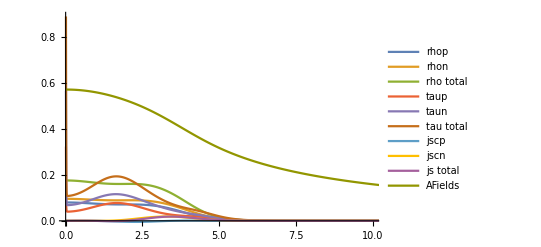

```mathematica
Show[ListPlot[DensitiesFieldsForPlotting,PlotRange->{{0,10},All},PlotLegends->Table[ToString[names[[i]]],{i,1,Length[names]}],Joined->True]]
```

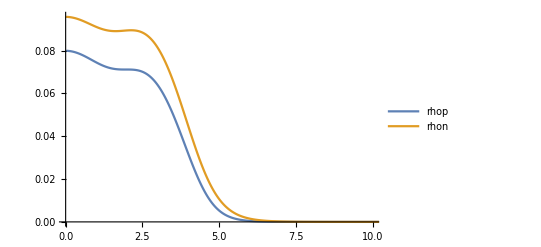

```mathematica
Show[ListPlot[DensitiesFieldsForPlotting[[1;;2]],PlotRange->{{0,10},All},PlotLegends->Table[ToString[names[[i]]],{i,1,2}],Joined->True]]
```

## Solving the differential equations for wave functions

```mathematica
ZeroVector=ConstantArray[0,Length[x]];
```

```mathematica
ga0=Array[gaval,len];
```

```mathematica
(*t00=-2483.45;
x00=0.77300;
t10=484.2300;
x10=-0.31700;
t20=-556.6900;
x20=-1;
t30=13757;
x30=1.2630;
W0=1.2630;
alpha0=1/6;*)

(*t40=76.73614*)
```

```mathematica
t00=-2078.3280232;
t10=239.4008120;
t20=1575.1195419;
t30=14263.6462470;
x00=0.05375692;
x10=-5.07723238;
x20=-1.36650561;
x30=-0.16249117;
W0=142.6330444;
sig0=0.27001801;
```

```mathematica
(*The following function takes a list of the form [t0,x0,t1,x1,t2,x2,t3,x3,W,sig]_0 and returns the rules to substitute those variables by those values*)
```

```mathematica
ApplyingRulesParameters[paramvalueslist_]:={t0->paramvalueslist[[1]],x0->paramvalueslist[[2]],t1->paramvalueslist[[3]],x1->paramvalueslist[[4]],t2->paramvalueslist[[5]],x2->paramvalueslist[[6]],t3->paramvalueslist[[7]],x3->paramvalueslist[[8]],W->paramvalueslist[[9]],sig->paramvalueslist[[10]]};
```

```mathematica
ApplyingRulesParameters[{t00,x00,t10,x10,t20,x20,t30,x30,W0,sig0}]
```

{t0→-2078.33,x0→0.0537569,t1→239.401,x1→-5.07723,t2→1575.12,x2→-1.36651,t3→14263.6,x3→-0.162491,W→142.633,sig→0.270018}

```mathematica
NormEq=(ga0.ga0)*dx-1;
```

```mathematica
EqWFSolver[ProtOrNeutr_,ListOfParameters_,DensitiesAndfields_,guess_,ChiValue_]:=Module[{EqsFGIn,FinalEqsFGIn,sol2In},

(*ProtOrNeutr=1 if protons, =0 if neutrons*)

(*ListOfParameters0={t0->-2078.3280232,x0->0.05375692,t1->239.400812,x1->-5.07723238,t2->1575.1195419,x2->-1.36650561,t3->14263.646247,x3->-0.16249117,W->142.6330444,sig->0.27001801};*)

(*DensitiesAndfields={rhop,rhon,rho total,taup,taun,tau total,jscp,jscn,jstotal, Afield}*)

(*guess={guessG,GuessEnergy}}*)

If[ChiValue >= 0,
L0=ChiValue,
L0=-1-ChiValue
];

J0=Abs[ChiValue]-1/2;

If[ProtOrNeutr==1,

If[Mod[L0,2]==0,


EqsFGIn={eqnsP}/.Join[ListOfParameters,{

J->J0,L->L0,

rhop->DensitiesAndfields[[1]],rhon->DensitiesAndfields[[2]],rhotot->DensitiesAndfields[[3]],taup->DensitiesAndfields[[4]],taun->DensitiesAndfields[[5]],tautot->DensitiesAndfields[[6]],jscp->DensitiesAndfields[[7]],jscn->DensitiesAndfields[[8]],jsctot->DensitiesAndfields[[9]],AField->DensitiesAndfields[[10]],
rho->DensitiesAndfields[[1]],tau->DensitiesAndfields[[4]],jsc->DensitiesAndfields[[7]],

rhop0->RHOP0,  rhon0->RHON0,rho0->RHOP0,

(*The final substitutions above, rho-> , tau-> , jsc->   changes if we have protons or neutrons*)

D1->D1MatOdd,D2->D2MatOdd,Dd1->D1MatFieldsEven,Dd2->D2MatFieldsEven,Ddd1->D1MatOdd,r->x,WF->ga0,χ->ChiValue,e->e0}],



EqsFGIn={eqnsP}/.Join[ListOfParameters,{

J->J0,L->L0,

rhop->DensitiesAndfields[[1]],rhon->DensitiesAndfields[[2]],rhotot->DensitiesAndfields[[3]],taup->DensitiesAndfields[[4]],taun->DensitiesAndfields[[5]],tautot->DensitiesAndfields[[6]],jscp->DensitiesAndfields[[7]],jscn->DensitiesAndfields[[8]],jsctot->DensitiesAndfields[[9]],AField->DensitiesAndfields[[10]],
rho->DensitiesAndfields[[1]],tau->DensitiesAndfields[[4]],jsc->DensitiesAndfields[[7]],
(*The final substitutions above, rho-> , tau-> , jsc->   changes if we have protons or neutrons*)

rhop0->RHOP0,  rhon0->RHON0,rho0->RHOP0,

D1->D1MatEven,D2->D2MatEven,Dd1->D1MatFieldsEven,Dd2->D2MatFieldsEven,Ddd1->D1MatOdd,r->x,WF->ga0,χ->ChiValue,e->e0}]



]



,


If[Mod[L0,2]==0,
EqsFGIn={eqnsN}/.Join[ListOfParameters,{
J->J0,L->L0,
rhop->DensitiesAndfields[[1]],rhon->DensitiesAndfields[[2]],rhotot->DensitiesAndfields[[3]],taup->DensitiesAndfields[[4]],taun->DensitiesAndfields[[5]],tautot->DensitiesAndfields[[6]],jscp->DensitiesAndfields[[7]],jscn->DensitiesAndfields[[8]],jsctot->DensitiesAndfields[[9]],
rho->DensitiesAndfields[[2]],tau->DensitiesAndfields[[5]],jsc->DensitiesAndfields[[8]],

rhop0->RHOP0,  rhon0->RHON0,rho0->RHON0,

D1->D1MatOdd,D2->D2MatOdd,Dd1->D1MatFieldsEven,Dd2->D2MatFieldsEven,Ddd1->D1MatOdd,r->x,WF->ga0,χ->ChiValue}],

EqsFGIn={eqnsN}/.Join[ListOfParameters,{
J->J0,L->L0,
rhop->DensitiesAndfields[[1]],rhon->DensitiesAndfields[[2]],rhotot->DensitiesAndfields[[3]],taup->DensitiesAndfields[[4]],taun->DensitiesAndfields[[5]],tautot->DensitiesAndfields[[6]],jscp->DensitiesAndfields[[7]],jscn->DensitiesAndfields[[8]],jsctot->DensitiesAndfields[[9]],
rho->DensitiesAndfields[[2]],tau->DensitiesAndfields[[5]],jsc->DensitiesAndfields[[8]],


rhop0->RHOP0,  rhon0->RHON0,rho0->RHON0,
D1->D1MatEven,D2->D2MatEven,Dd1->D1MatFieldsEven,Dd2->D2MatFieldsEven,Ddd1->D1MatOdd,r->x,WF->ga0,χ->ChiValue}]



]


];



FinalEqsFGIn=Join[Thread[EqsFGIn[[1]]==ZeroVector],{NormEq==0}];



sol2In=FindRoot[FinalEqsFGIn,Transpose[{Join[{lambda},ga0],Join[{guess[[2]]},guess[[1]]]}],PrecisionGoal->20,MaxIterations->500]; 
(*sol2ProtIn=FindRoot[FinalEqsProtons,Transpose[{Join[{Ea},fa0,ga0],Join[{10},ListOfWP[[1]][[2]],ListOfWP[[1]][[3]]]}],PrecisionGoal->20,MaxIterations->500]; *)



(*{Energy,F,G}}*)

{ga0/.sol2In,lambda/.sol2In[[1]]}



]
```

```mathematica
Solutions0=EqWFSolver[1,ApplyingRulesParameters[{t00,x00,t10,x10,t20,x20,t30,x30,W0,sig0}],DensitiesAndFieldsBuilder[{ListOfWP,ListOfWN},ListOfChis],{ListOfWP[[2]],30},ListOfChis[[1]][[2]]];
```

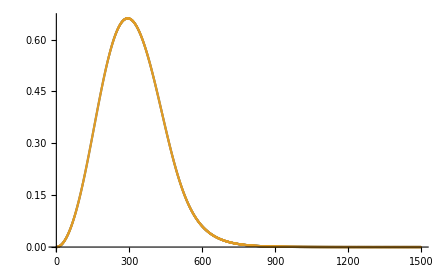

```mathematica
ListPlot[{Solutions0[[1]],ListOfWP[[2]]}]
```

```mathematica
Solutions0[[2]]
```

29.887

```mathematica
ProtonLevelsEnergy
```

{37.75,29.91,29.11,19.76,19.21,16.05}

```mathematica
(*This function takes as inputs the parameters and the densities (and some guesses) and gives back the energies and WF of all the states for the nucleus. The function defined next iterates to find a self consistent solution.*)
```

```mathematica
AllWFEquationsSolver[ListOfParameters_,DensitiesAndfields_,guessList_,ChiValueList_]:=Module[{in,solProtons,solNeutrons,EnergiesIn,ListOfWFsIn},
(*ListOfParameters0={t0->-2078.3280232,x0->0.05375692,t1->239.400812,x1->-5.07723238,t2->1575.1195419,x2->-1.36650561,t3->14263.646247,x3->-0.16249117,W->142.6330444,sig->0.27001801};*)

(*DensitiesAndfields={rhop,rhon,rho total,taup,taun,tau total,jscp,jscn,jstotal, Afield}*)

(*guessList={
{{Guess protons WF}, {Guess protons Energies}}


{{Guess neutrons WF}, {Guess neutrons Energies}},
....
}
*)


(*ChiValueList= {
{chiproton1,chiproton2,....}
,
{chineutron1,chineutron2,...}}
*)

solProtons={};
solNeutrons={};


(*ProtonLoop*)
For[in=1,in<=Length[ChiValueList[[1]]],in++,
AppendTo[solProtons,
EqWFSolver[1,ListOfParameters,DensitiesAndfields,{guessList[[1]][[1]][[in]],guessList[[1]][[2]][[in]]},ChiValueList[[1]][[in]]]
]
];

(*NeutronLoop*)
For[in=1,in<=Length[ChiValueList[[2]]],in++,
AppendTo[solNeutrons,

EqWFSolver[0,ListOfParameters,DensitiesAndfields,{guessList[[2]][[1]][[in]],guessList[[2]][[2]][[in]]},ChiValueList[[2]][[in]]]
]
];

EnergiesIn={
Table[solProtons[[in]][[2]],{in,1,Length[solProtons]}],
Table[solNeutrons[[in]][[2]],{in,1,Length[solNeutrons]}]
};

ListOfWFsIn={
Table[solProtons[[in]][[1]],{in,1,Length[solProtons]}],
Table[solNeutrons[[in]][[1]],{in,1,Length[solNeutrons]}]

};


{ListOfWFsIn,EnergiesIn}

];
```

```mathematica
GuessToTry={{gprotons,ProtonLevelsEnergy},{gneutrons,NeutronLevelsEnergy}};
```

```mathematica
Solutions0All=AllWFEquationsSolver[ApplyingRulesParameters[{t00,x00,t10,x10,t20,x20,t30,x30,W0,sig0}],DensitiesAndFieldsBuilder[{ListOfWP,ListOfWN},ListOfChis],GuessToTry,ListOfChis];
```

```mathematica
Sols0ToPlotProts=Solutions0All[[1]][[1]];
```

```mathematica
Sols0ToPlotNeutrs=Solutions0All[[1]][[2]];
```

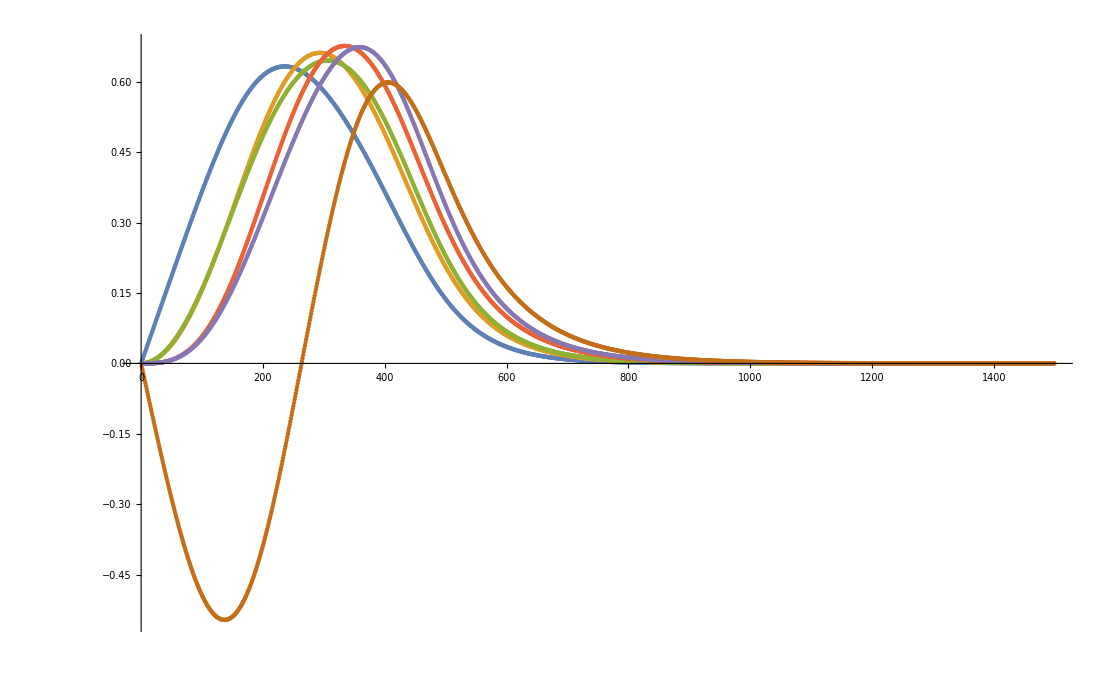

```mathematica
Show[ListPlot[Sols0ToPlotProts,Joined->True,PlotRange->All],ListPlot[gprotons]]
```

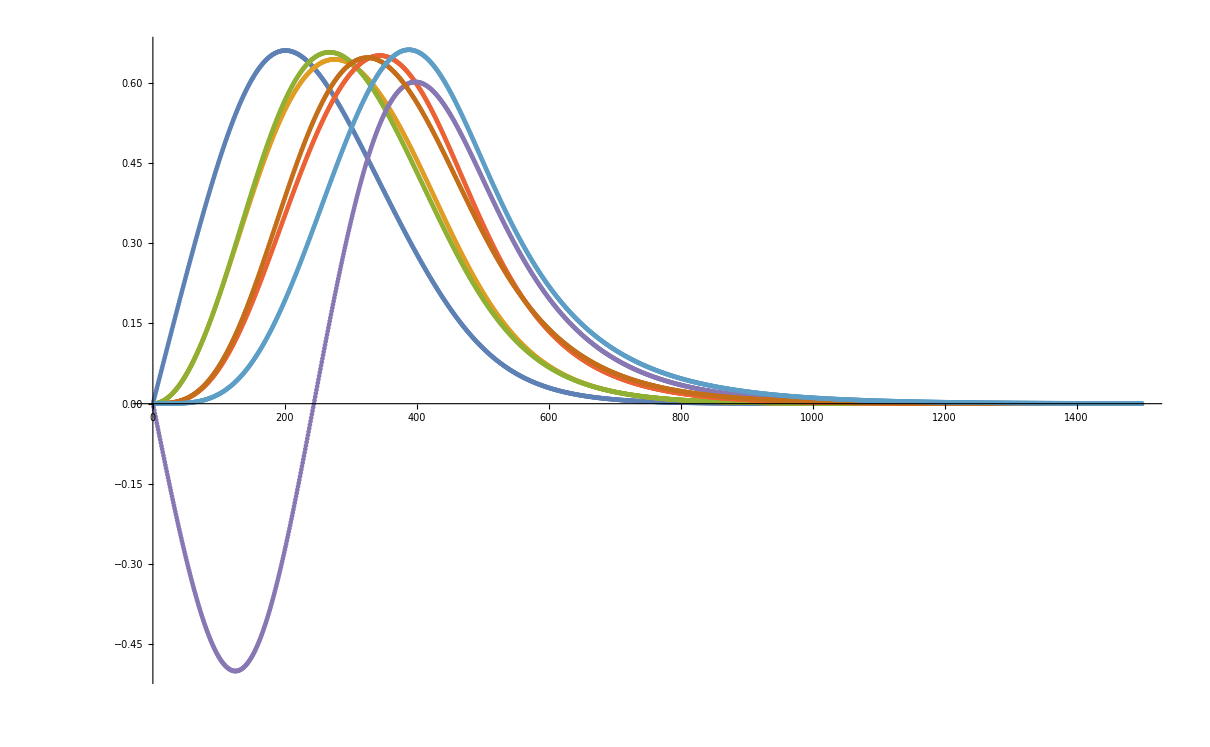

```mathematica
Show[ListPlot[Sols0ToPlotNeutrs,PlotRange->All,Joined->True],ListPlot[gneutrons]]
```

```mathematica
Solutions0All[[2]]
```

{{37.7288,29.887,29.0844,19.738,19.1936,16.0313},{36.7198,27.3758,25.754,17.7097,15.5345,14.389,8.08615}}

```mathematica
ListOfEnergies
```

{{37.75,29.91,29.11,19.76,19.21,16.05},{36.719,27.375,25.75,17.71,15.53,14.38,8.09}}

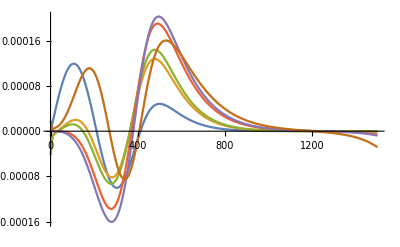

```mathematica
Show[ListPlot[Sols0ToPlotProts-gprotons,Joined->True,PlotRange->All]]
```

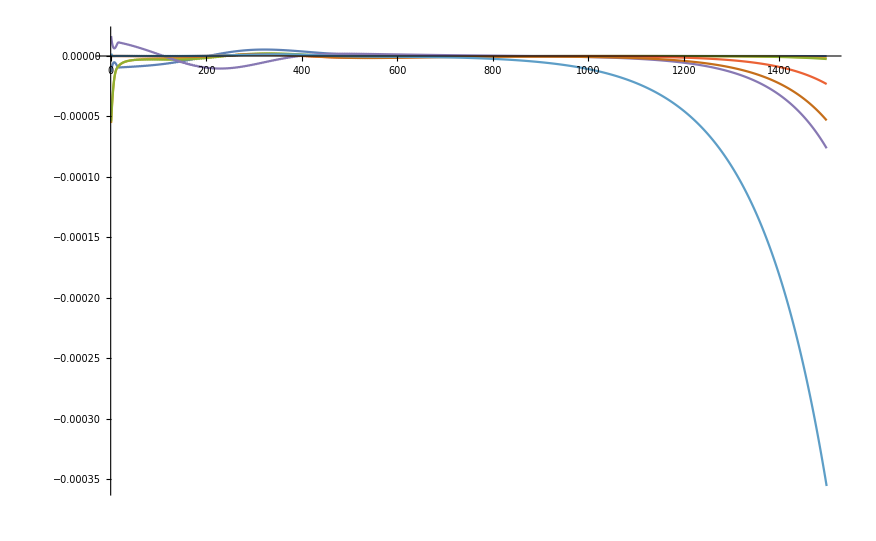

```mathematica
Show[ListPlot[Sols0ToPlotNeutrs-gneutrons,Joined->True,PlotRange->All]]
```

```mathematica
MaxIterationsDFT=40;
```

```mathematica
IterativeSolver[ListOfParameters_,guessList_,ChiValueList_]:=Module[{Solutions0In,DensitiesAndFieldsIn,WFandChis,IJin,iKIn
},
(*ListOfParameters0={t0->-2078.3280232,x0->0.05375692,t1->239.400812,x1->-5.07723238,t2->1575.1195419,x2->-1.36650561,t3->14263.646247,x3->-0.16249117,W->142.6330444,sig->0.27001801};*)

(*guessList={
{{Guess protons WF}, {Guess protons Energies}}


{{Guess neutrons WF}, {Guess neutrons Energies}},
....
}
*)


(*ChiValueList= {
{chiproton1,chiproton2,....}
,
{chineutron1,chineutron2,...}}
*)


DensitiesAndFieldsIn=DensitiesAndFieldsBuilder[{guessList[[1]][[1]],guessList[[2]][[1]]},ChiValueList];


Solutions0In=AllWFEquationsSolver[ListOfParameters,DensitiesAndFieldsIn,guessList,ChiValueList];



For[IJin=1,IJin<=MaxIterationsDFT,IJin++,
(*Print[Solutions0In[[2]]];*)

DensitiesAndFieldsIn=DensitiesAndFieldsBuilder[Solutions0In[[1]],ChiValueList]*0.2+0.8*DensitiesAndFieldsIn;




Solutions0In=AllWFEquationsSolver[ListOfParameters,DensitiesAndFieldsIn,{ {Solutions0In[[1]][[1]],Solutions0In[[2]][[1]]}  ,{Solutions0In[[1]][[2]],Solutions0In[[2]][[2]]}   },ChiValueList];



(*Solutions0In=AllWFEquationsSolver[ListOfParameters,DensitiesAndFieldsIn,{ {Solutions0In[[1]][[1]],guessList[[1]][[2]]}  ,{Solutions0In[[1]][[2]],guessList[[2]][[2]]}   },ChiValueList];*)

];

Solutions0In

]
```

```mathematica
Timing[SolutionsFinal0=IterativeSolver[ApplyingRulesParameters[{t00,x00,t10,x10,t20,x20,t30,x30,W0,sig0}],GuessToTry,{ProtonLevelsKappa,NeutronLevelsKappa}];]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{126.969,Null}

```mathematica
SolutionsFinal0[[2]]
```

{{37.7316,29.8909,29.088,19.742,19.1964,16.0311},{36.7193,27.3753,25.7539,17.7098,15.5363,14.3901,8.087}}

```mathematica
SolutionsFinal0[[2]]
```

{{37.7316,29.8909,29.088,19.742,19.1964,16.0311},{36.7193,27.3753,25.7539,17.7098,15.5363,14.3901,8.087}}

```mathematica
SolutionsFinal0[[2]]
```

{{37.7316,29.8909,29.088,19.742,19.1964,16.0311},{36.7193,27.3753,25.7539,17.7098,15.5363,14.3901,8.087}}

```mathematica
ListOfEnergies
```

{{37.75,29.91,29.11,19.76,19.21,16.05},{36.719,27.375,25.75,17.71,15.53,14.38,8.09}}

```mathematica
Length[x]
```

1499

```mathematica
DensSols0=DensitiesAndFieldsBuilder[SolutionsFinal0[[1]],ListOfChis];
```

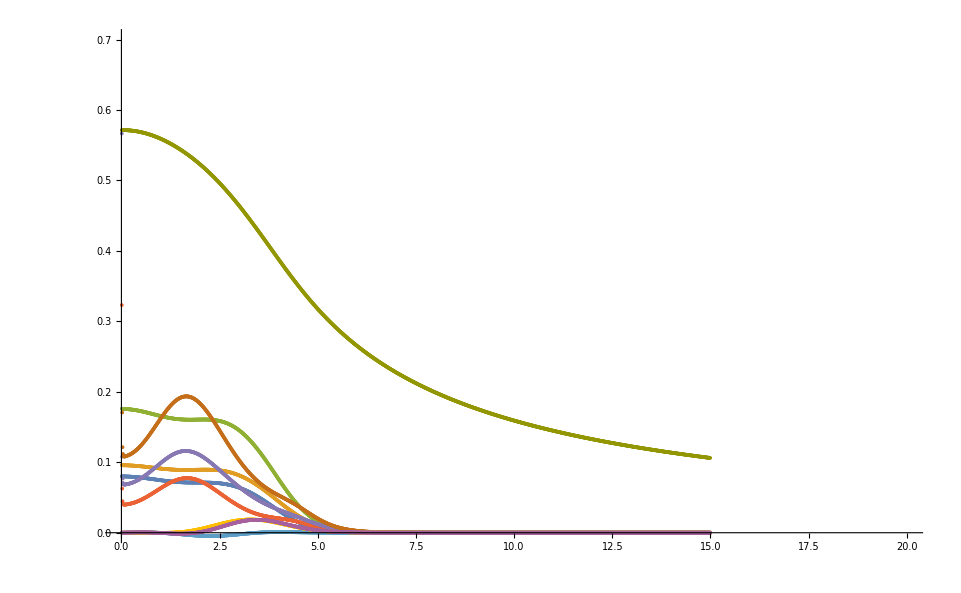

```mathematica
Show[ListPlot[Table[Transpose[{x,DensSols0[[i]]}],{i,1,Length[DensSols0]}],Joined->True,PlotRange->{{0,20},{0,0.7}}],ListPlot[DensitiesFieldsForPlotting]]
```

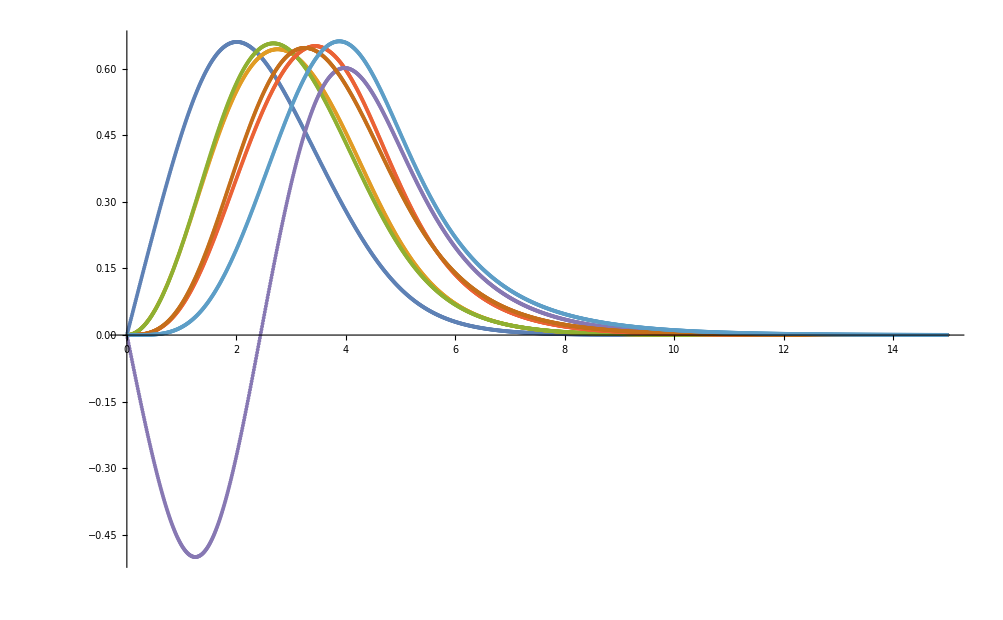

```mathematica
Show[ListPlot[Table[Transpose[{x,SolutionsFinal0[[1]][[2]][[i]]}],{i,1,Length[SolutionsFinal0[[1]][[2]]]}],PlotRange->All,Joined->True],ListPlot[Table[Transpose[{x,gneutrons[[i]]}],{i,1,Length[gneutrons]}]]]
```

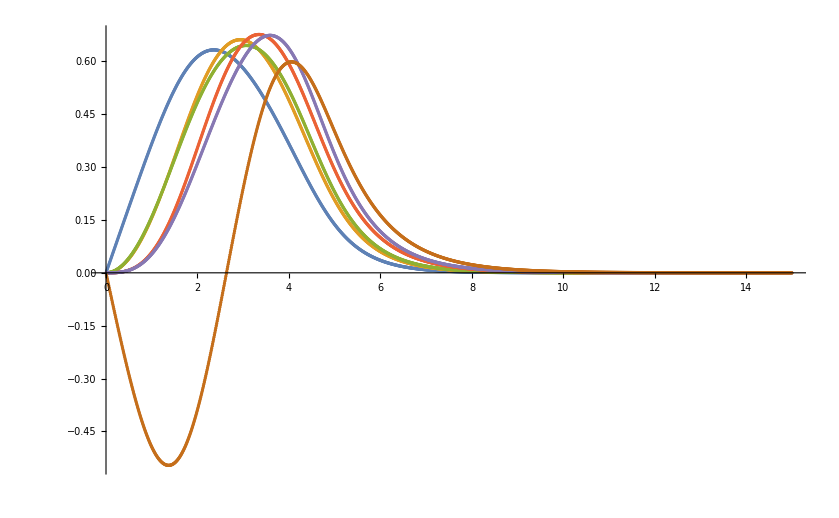

```mathematica
Show[ListPlot[Table[Transpose[{x,SolutionsFinal0[[1]][[1]][[i]]}],{i,1,Length[SolutionsFinal0[[1]][[1]]]}],PlotRange->All,Joined->True],ListPlot[Table[Transpose[{x,gprotons[[i]]}],{i,1,Length[gprotons]}]]]
```

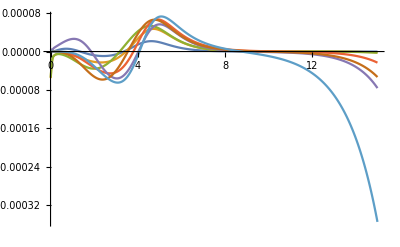

```mathematica
Show[ListPlot[Table[Transpose[{x,SolutionsFinal0[[1]][[2]][[i]]-gneutrons[[i]]}],{i,1,Length[SolutionsFinal0[[1]][[2]]]}],PlotRange->All,Joined->True]]
```

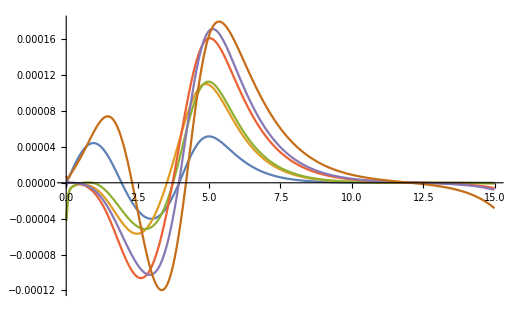

```mathematica
Show[ListPlot[Table[Transpose[{x,SolutionsFinal0[[1]][[1]][[i]]-gprotons[[i]]}],{i,1,Length[SolutionsFinal0[[1]][[1]]]}],PlotRange->All,Joined->True]]
```

```mathematica
(*Ok, everything seems to be agreeing well in comparison to the true solver from Fortran*)
```

## Galerkin approach

```mathematica
(*First we need to define a basis, the next are the 50 random values of the NM parameters so we can then do SVD on top of them*)
```

```mathematica
ParametersKyle={{-15.898245417699494,197.05534472645257,1.2989103479303297,0.15057647035628854,30.1104616077847,162.04657540886438,{-44.55987394692793,-123.45365717423603},{-101.09065136670942,-44.96071544991546}},{-14.836391045454567,184.1334546061099,0.9540018887020836,0.15473401838877485,31.101484187554274,130.53689559542192,{-43.3732093819222,-142.92529212894036},{-95.60658039416211,-25.12909350534732}},{-15.941041259728832,189.60440797443778,1.085624794101616,0.14031997271488053,27.15426140049278,179.18676397666428,{-44.43268026764706,-122.3912033912739},{-85.01566128082852,-18.947557304024016}},{-16.31399517394407,240.02833175702946,1.3192494942673678,0.17542070982704314,26.90250619746839,27.72540897755305,{-47.10077178185533,-106.1603407480236},{-74.06209567385801,-45.93176266160552}},{-16.35469658071899,202.37632316613713,1.2012689601305553,0.14658957214738047,31.99411375872198,50.31137133983192,{-42.29331217248074,-102.52721984665254},{-77.8372982949126,-34.16152263907632}},{-15.46710111732377,230.0612933770236,1.3560473522973782,0.1591432884844515,28.645921517070455,139.57743580821068,{-46.70102843228325,-98.1748039012815},{-66.59814230418267,-35.92353953783515}},{-15.854070476266154,217.06790370025044,0.7305755175518084,0.15705045992950709,28.082314117498093,23.42891334671753,{-51.20122550197661,-144.2230954457963},{-79.84299935010279,-23.547237396723816}},{-15.817958557062111,208.22953936231048,0.9261254084007888,0.17420172503422207,26.374232481462,111.35101982515023,{-51.02353862149843,-141.4074997225736},{-76.63158698990262,-29.33218659232667}},{-15.558325008184232,221.26159425696918,1.0679436428323739,0.16855200949375404,31.46090050532266,156.06820052275754,{-50.5571312591533,-150.54302279930758},{-78.28594135046131,-26.038459532797233}},{-14.587263628928554,252.709564245315,1.18405962447416,0.15363229275263965,30.669511893767858,92.70724255748954,{-42.725048324373915,-91.84395815549595},{-72.00462182607072,-37.80675602330734}},{-14.62386766484323,228.97594611052762,1.2549306611251814,0.17069893821872278,28.839368460301905,101.1901857817844,{-54.864397192931115,-154.29174572909778},{-67.70803700258051,-24.12515523588322}},{-14.985437905969471,232.1379595612931,0.9180249719599948,0.1702338075045055,31.667284082493182,97.1023126286546,{-42.61869734608513,-163.62244285599473},{-99.95821115273556,-49.56856638984949}},{-15.914205464607138,210.2398142598043,1.3771912876314913,0.17752245565158567,27.502360800417186,159.4992139757918,{-48.78556017681477,-107.21002830055644},{-102.60957309798121,-46.818576651782706}},{-15.373313331364765,239.44925017019813,1.1298869585649778,0.14516906016427944,27.28940650331392,64.87970444034076,{-53.385749262341164,-128.1107023433731},{-82.36437057550661,-20.721451389301272}},{-16.21460885630979,247.24398715832484,0.9730384277685947,0.1636460710826449,30.228735907601827,82.52020483283101,{-44.8206635627184,-130.03375597465586},{-98.5031395349688,-32.676997059952114}},{-15.077281106968993,193.87258394125558,0.7432112893393479,0.14585382836692196,29.93011903106147,148.4780816064094,{-43.800226901335165,-137.2888203988934},{-104.635266544162,-47.71127980386719}},{-16.060543508785106,166.11873728102685,1.220678306602784,0.1646863062544377,29.39411606613831,165.44257341750404,{-47.26620374204826,-161.66642884552698},{-71.17758425081057,-19.909770436472417}},{-15.733737182451717,201.67608033651243,1.0185651795896713,0.169574535461459,29.13766320151398,107.38667691731195,{-47.582924735756414,-157.48314486478844},{-65.3861064332987,-39.451632605906426}},{-15.310990360626569,204.8712283604406,0.9507996465728856,0.1777178381584821,31.565056917125315,23.035381298222738,{-53.14955024016143,-125.5392888618318},{-58.55877715756132,-29.704636176539914}},{-16.39207229602848,161.7736242227845,0.8216089833791375,0.14222204060706004,26.064153731699797,151.72312924090642,{-46.04133778911747,-139.28015339869032},{-94.58437148295175,-27.174451244722828}},{-15.29174652194102,194.5860919724009,0.8348610548433482,0.14138177681077185,26.35954305164656,115.44145552967802,{-43.023025315344654,-146.70576834934636},{-69.60340542841645,-42.08742188923649}},{-16.49910279204444,191.01931894803,1.024280569964799,0.16693283261981626,31.781600307909052,62.41804146729842,{-49.421490201691796,-95.21753202089307},{-60.81585667153895,-22.248230634814345}},{-15.16044630787077,237.05864945368455,1.3989245428471104,0.15602067222278046,27.96775878924653,174.2407846656138,{-40.77590440522934,-132.2512606910708},{-57.429860185722106,-31.275616490687273}},{-16.22080839555061,171.54577827939045,1.2347954286214615,0.14787208359185083,28.50903842071095,89.05504327408026,{-54.236226353554166,-108.27601850681725},{-80.45399667517788,-26.276684104520985}},{-15.433696905866023,162.96257098448794,0.9907628787398489,0.17955960269672724,28.894967072011156,170.26732360650965,{-44.1613825736392,-149.34857669863},{-89.02129781295115,-49.07107449437624}},{-16.14237119084189,226.31947432397862,0.8560704185478252,0.16211269372248932,30.858353840341763,127.87474632622626,{-51.92461054523693,-159.86529052458226},{-64.32623067196548,-45.403076622932595}},{-14.788116641014817,258.3633586352138,0.7088381005432587,0.17499145310918998,30.547292822624485,70.78321960847714,{-41.21711847633817,-94.0540334924491},{-59.629596062295896,-30.585744131533016}},{-15.240855820160187,187.78369252651535,1.1575898556116826,0.15187297729172788,30.32754633999386,86.70794586578224,{-51.527927237509026,-96.71768606773797},{-68.0944164554908,-38.13374850551291}},{-14.72431680679285,248.98550064203715,1.092896162891142,0.17168841200044926,29.779189558035032,133.33486172229772,{-52.33490478327811,-139.91921308312843},{-63.29486934544641,-43.80428775825359}},{-14.895196611871285,165.0881949392821,1.0605742657519712,0.17845537469503353,26.545580362343223,36.10810969862119,{-41.83540658505029,-100.49348122324821},{-97.75582337999953,-27.794494553803755}},{-16.27607227126614,207.23090535317846,1.1459847155320202,0.15034203981486827,27.646868434596026,32.16866458456494,{-45.86860199258909,-114.3503136367753},{-86.17797785217581,-21.411784388632938}},{-16.43397844654829,174.0233940486975,1.20917275870888,0.1601331358838506,31.30396187215881,94.31604057754315,{-53.97735034473382,-163.35095489898066},{-83.1200545236611,-16.218172203902355}},{-16.115370839254084,245.11318450662822,0.8979646208755443,0.16306057175405342,29.974636655222845,56.35031558010014,{-53.6989023280813,-113.20369515741197},{-81.53445304653755,-48.57695099331492}},{-15.514103572663817,234.29149646544562,0.7938750460376618,0.14846263807711244,28.586451974881726,33.61667641365116,{-48.4584277339006,-133.63882871162676},{-75.99460094456526,-36.935836103821394}},{-15.588265863081707,169.10392128220423,1.3082645000667892,0.14291752263331303,27.034647051628472,45.95784035430809,{-41.61009065263177,-117.39847903673308},{-91.77466293570996,-17.298595208159178}},{-14.573926322194158,250.6478512143899,1.2858071742709103,0.14947710826204474,31.180305564850162,172.10795014338282,{-49.927819893633306,-101.77105640003461},{-62.307590211171444,-19.687509692124863}},{-14.531128266262547,212.1436665696737,0.8924631160020283,0.16638680817305954,30.722764071946195,59.01637627280371,{-40.31342244825367,-116.98202150822041},{-88.22349004079867,-40.5249194825422}},{-16.027709904339595,182.52329827874007,1.113331863662623,0.1553368822944258,26.194087374164067,120.49832092682621,{-54.40390579032378,-131.01168120021273},{-87.37264431231469,-39.85464715923565}},{-14.91002247400075,257.4837903952946,1.3625905322317875,0.165079131652198,29.718224833692013,141.83455486683607,{-49.02541466949089,-152.3568320081024},{-84.67210374135794,-32.358176962763366}},{-15.117533256386459,225.53529333817536,1.172405305794824,0.1615663925340071,28.193185334389405,124.34613969577288,{-40.152616952217244,-103.51265360391525},{-90.00709414965081,-41.39486586471098}},{-14.954529918057782,176.52409695963698,0.850915032272336,0.17633432886851153,27.871972677170323,78.9966708460299,{-45.415700703070414,-155.2744017401335},{-103.54291150307475,-23.346009158128904}},{-14.681414894611871,222.27935968872424,1.3344196292941892,0.15813619998156567,29.009080763923432,54.8711036671939,{-40.968200711352225,-126.66364913999669},{-70.32936048608775,-43.28490784341156}},{-15.046346802673217,214.19276034554431,0.8019058955691217,0.16750672437723893,28.375377475682733,76.51464964340255,{-47.85607783195066,-90.29789414350608},{-61.2102202364871,-15.119722495546938}},{-15.685404258314732,255.66103898424424,1.0417194056029446,0.17202835818052967,29.57246573253316,43.42100118541601,{-52.695657128982525,-110.31574635264582},{-96.9456175891189,-36.29294115052807}},{-15.643261535412021,199.58835003929778,0.9973768058988226,0.1445227006634703,27.33520867328347,118.9173101844682,{-48.197113902845786,-135.91454216193569},{-93.80409579537083,-28.33322528473942}},{-15.752112520635821,242.4543455963303,0.726039683231485,0.15295620561900836,26.79214786480993,73.90659384804366,{-49.828129488144924,-157.76023768939402},{-56.46187405659248,-33.84767170261344}},{-15.993178944499169,172.1011318811639,1.2717857819740923,0.1522314290529252,30.982064831788062,136.66827083214585,{-52.28123928929543,-120.99675088895614},{-92.24446970740294,-42.93484013785961}},{-15.386703400307574,180.745345574741,0.7763296190441833,0.15963221709080683,27.71262121827065,145.75837584050072,{-50.33091582205105,-147.81736456644808},{-100.66436514190963,-17.074374228404068}},{-14.773227310180804,179.89512128244627,0.8818752792600867,0.1432333753749224,29.2547123837321,39.31707762126154,{-46.39465862299109,-111.43150877174804},{-55.76327743224646,-35.1641363938083}},{-15.208648464069833,219.5599636872762,0.7619836479357016,0.1735339661973535,26.681249122481308,103.20071743575764,{-45.38145041527043,-118.68227006767805},{-73.19645862863788,-17.994033137255443}}};
```

```mathematica
BasisNeutronsG={};
BasisProtonsG={};
```

```mathematica
NMConstants0={-15.8,220.0,0.992423332283364,0.158706769332587,28.986789057772100,40.004790480413600,{-45.1351310222373,-145.382167908057},{-74.0263331764599,-35.6582611147917}};
```

```mathematica
TableOfAlphas={};
```

```mathematica
TableOfEverything={};
```

```mathematica
ListOfEnergiesResults={};
```

```mathematica
(*Training for 50 values of the parameters that Kyle gave us*)
```

```mathematica
For[Kin=1,Kin<=Length[ParametersKyle],Kin++,

Print[Kin];


NMConstantsNew=ParametersKyle[[Kin]];


TempResults=IterativeSolver[ApplyingRulesParameters[NMConstantsToParameters[NMConstantsNew]],GuessToTry,{ProtonLevelsKappa,NeutronLevelsKappa}];

AppendTo[TableOfEverything,ApplyingRulesParameters[NMConstantsToParameters[NMConstantsNew]]];
AppendTo[BasisNeutronsG,TempResults[[1]][[2]]];
AppendTo[BasisProtonsG,TempResults[[1]][[1]]];

AppendTo[ListOfEnergiesResults,TempResults[[2]]]
]
```

1

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

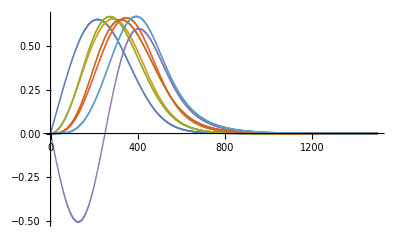

```mathematica
ListPlot[BasisNeutronsG[[1]]]
```

```mathematica
Length[BasisNeutronsG]
```

10

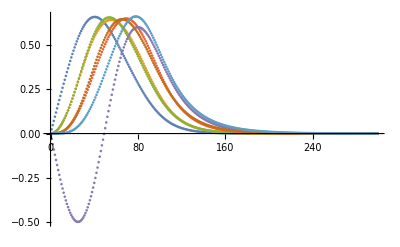

```mathematica
ListPlot[BasisNeutronsG[[2]]]
```

```mathematica
BasisNeutronsGFull=BasisNeutronsG;
```

```mathematica
BasisProtonsGFull=BasisProtonsG;
```

```mathematica
Export["BasisNeutronsGFull.txt",BasisNeutronsGFull]
```

BasisNeutronsGFull.txt

```mathematica
Export["BasisProtonsGFull.txt",BasisProtonsGFull]
```

BasisProtonsGFull.txt

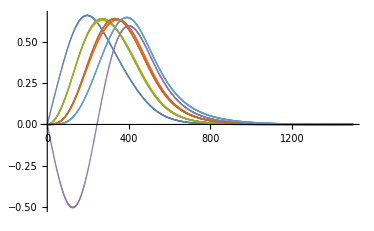

```mathematica
ListPlot[BasisNeutronsGFull]
```

```mathematica
(*Very annoying, but I had to remove by hand the following values of the parameters which gave convergence issues from the true DFT solver. I guess with more time we could find different seeds to be able to make them converge, while for RB there is almost never a problem with that xD*)
```

```mathematica
ListOfProblems={7,16,46,26,41,48};
```

```mathematica
BasisNeutronsG={};
```

```mathematica
BasisProtonsG={};
```

```mathematica
MemberQ[ListOfProblems,7]
```

True

```mathematica
For[i=1,i<=Length[BasisProtonsGFull],i++,

If[MemberQ[ListOfProblems,i],,

AppendTo[BasisNeutronsG,BasisNeutronsGFull[[i]]]; 

AppendTo[BasisProtonsG,BasisProtonsGFull[[i]]]]


]
```

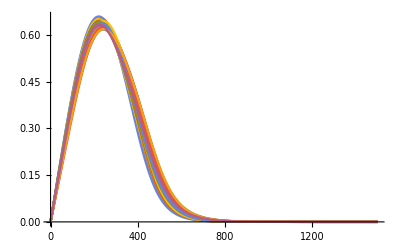
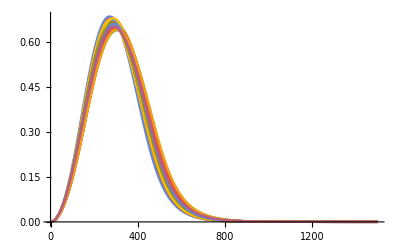
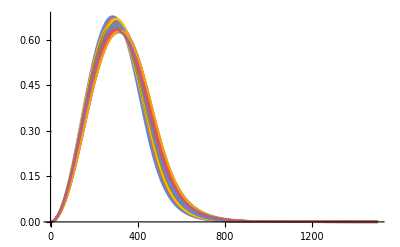
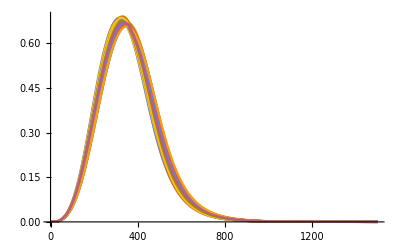
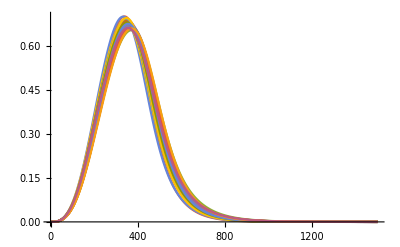
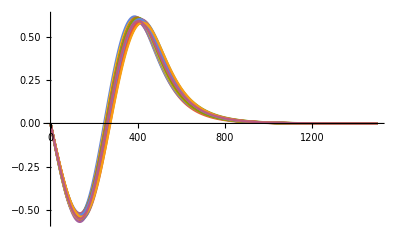

```mathematica
Table[ListPlot[Transpose[BasisProtonsG][[j]],Joined->True,PlotRange->All],{j,1,6}]
```

```mathematica
ListOfEnergiesResultsFull=ListOfEnergiesResults
```

{{{42.4152,30.539,31.8921,16.6287,19.934,13.3539},{48.742,36.9451,34.5305,24.7323,19.6759,19.362,12.9959}},{{33.1602,26.2009,24.5987,17.0071,14.857,13.1014},{35.6067,26.6791,26.2346,17.4496,16.4669,16.3458,8.26711}},{{33.7681,25.94,24.5032,16.0251,13.9828,11.7117},{41.2377,31.5116,31.6906,21.4725,20.2455,21.372,11.608}},{{47.7501,34.2809,36.633,18.7672,24.1075,16.1979},{52.385,38.7548,35.2336,24.7839,18.3112,17.0289,11.5242}},{{43.0244,33.2112,33.5485,21.27,22.6826,17.5047},{42.9282,31.7701,30.3304,20.2021,16.6385,16.8052,8.93844}},{{44.151,31.4693,32.6078,16.9174,19.7677,13.5934},{50.8918,37.7594,35.9686,24.2051,19.4245,19.9712,11.279}},{{13.3894,11.1792,7.211,5.73918,1.70202,13.3894},{-0.936665,-10.1001,-3.46637,-2.44501,-0.936665,-2.47953,11.4738}},{{33.746,26.0635,24.8669,16.3128,14.9063,13.2096},{37.5373,28.3299,27.2977,18.888,17.7706,16.7778,9.49833}},{{36.6434,28.1225,26.5182,17.4504,15.3191,13.3508},{41.1328,30.3538,29.9039,19.4172,18.1135,18.2299,8.87261}},{{40.0883,29.495,30.6607,16.8899,19.7972,13.8974},{42.3259,31.4112,29.3721,20.0746,15.84,15.4412,8.97254}},{{40.8442,30.7458,28.9949,18.5915,16.2653,13.8938},{45.6374,32.3732,32.2573,19.0902,17.417,18.422,6.76185}},{{35.7681,27.4854,27.7219,16.8474,18.3126,14.0373},{34.9687,26.7744,23.1074,18.2913,14.8858,11.3762,9.56882}},{{46.213,31.1217,33.9889,14.4576,20.5388,12.7527},{55.6241,41.8041,38.2434,27.7159,21.2265,19.9734,14.4618}},{{37.5431,29.5592,28.0032,19.4026,17.3126,14.845},{39.4741,28.7428,28.9222,17.722,16.4105,17.5864,7.05586}},{{37.2436,29.252,28.5814,19.0085,18.6099,15.4692},{37.3803,28.0952,26.6302,18.4714,16.4004,15.3921,8.83185}},{{16.984,9.12041,10.8875,0.0998987,12.3816,16.984},{0.559821,12.6024,8.90327,5.09207,0.559821,3.06272,13.1225}},{{38.9564,29.5383,27.3295,18.0055,14.7482,12.9464},{47.0852,34.7404,35.0649,22.3522,21.1979,22.5235,10.7652}},{{37.0751,28.2892,27.8318,17.4057,17.4305,14.2964},{39.7004,29.8575,27.7506,19.8093,17.341,15.6591,9.94474}},{{37.1277,28.8755,28.2001,18.755,18.2649,16.1474},{35.2656,25.5998,24.3094,15.7746,14.564,13.2179,6.14094}},{{28.6178,22.8403,21.5759,15.0091,13.2992,11.9484},{34.2557,27.2151,26.6792,19.8255,19.1817,18.6171,12.1866}},{{30.1794,23.7871,23.4803,15.3418,15.4866,12.6791},{31.7778,25.0846,23.1616,18.0175,16.1233,14.235,10.5796}},{{38.551,29.9855,29.3516,19.6429,19.0828,16.7047},{38.7508,28.5003,27.9815,18.0842,16.9265,16.7559,7.92624}},{{44.5548,32.6957,32.2504,18.3214,18.4277,12.6886},{52.4559,38.8283,37.8777,24.5767,20.0955,21.978,10.9575}},{{40.2523,30.3872,30.0584,18.9339,18.9119,15.6984},{44.0834,32.4469,31.939,20.69,18.624,19.2531,9.53979}},{{34.6912,24.5104,25.8082,12.6393,15.679,11.3049},{41.7878,32.5257,28.8313,23.1239,19.4781,16.0699,13.8095}},{{38.6915,28.7149,29.1356,15.6297,16.7254,14.8412},{40.3788,26.3869,22.3021,20.0994,25.9949,13.5789,11.9614}},{{30.5196,24.0096,23.8778,15.4394,15.8813,13.5449},{28.1373,21.846,19.8694,14.9448,13.5983,11.1941,7.4256}},{{38.9469,28.5881,29.6863,16.7396,19.3228,14.7932},{41.3407,30.6907,28.8058,19.8825,16.7122,15.7898,9.45801}},{{37.5699,27.1239,27.941,14.9366,17.1443,12.7791},{41.4902,30.8974,28.1799,20.1673,16.7095,14.6879,9.77289}},{{38.6731,29.083,28.9445,17.7062,18.1522,15.0411},{40.6476,29.7034,28.3169,18.6144,16.5795,15.6657,7.87685}},{{40.562,32.1344,30.8374,21.4786,19.897,16.8901},{41.4234,30.2476,30.1561,18.7541,17.0591,18.0898,7.61414}},{{40.7473,32.297,29.6601,21.6638,17.7319,16.443},{43.6323,31.3438,32.1288,19.0311,18.4194,20.0731,7.5318}},{{35.4185,26.5034,28.1954,16.047,19.7145,15.2381},{34.1396,26.3721,23.0142,18.3613,15.1597,11.7933,10.1329}},{{32.1784,26.089,25.4789,17.916,17.5876,15.2902},{28.9715,22.3957,20.699,15.2447,13.6791,11.9758,7.7184}},{{42.8375,33.6635,32.0629,22.1661,20.0482,16.6214},{45.5498,32.9246,33.3053,19.8643,17.6883,20.0215,7.38626}},{{39.5528,29.2675,28.4342,17.0338,16.1233,12.5458},{45.2985,33.0362,33.0954,20.415,18.1096,19.9493,8.34895}},{{34.7419,26.5453,27.1085,16.3554,18.1486,14.2452},{33.2094,25.1966,22.456,16.8407,14.1002,11.4639,8.24399}},{{36.7999,26.9774,27.4677,15.6215,17.0921,13.4603},{42.3783,32.1059,30.289,21.73,19.0531,17.9253,11.7104}},{{44.3313,32.7715,31.9472,18.8793,18.3234,13.6991},{50.4732,36.4915,35.5031,22.1995,18.5395,19.6721,8.80504}},{{40.1103,29.0057,30.4456,15.8571,19.3134,13.0843},{44.7197,33.7897,31.1779,22.4532,17.7068,16.7249,11.3378}},{{32.585,25.9599,23.5874,17.8962,14.4744,16.7945},{35.6866,27.1609,26.2913,16.3307,14.9083,15.3203,6.80439}},{{45.5628,33.7372,34.6895,19.3661,22.2213,14.9058},{48.908,35.9003,33.4035,22.3178,16.509,16.6194,9.30749}},{{30.9598,24.761,23.2638,16.4701,14.3733,13.3831},{31.4804,23.5825,23.6954,15.268,15.3121,15.2067,6.71768}},{{38.8864,29.1238,29.7262,17.6281,19.402,15.4719},{39.3378,29.0008,26.8875,18.5062,15.8339,14.1627,8.25414}},{{33.7752,26.4541,25.3868,17.0723,15.8095,13.4758},{36.9885,28.0449,27.4563,18.8044,17.412,17.3463,9.61409}},{{-3.48218,-20.3798,-4.83423,-8.47081,-2.77622,-39.2675},{-0.132166,2.16225,-6.21737,0.17818,-0.132166,-0.363225,0.0244666}},{{41.4177,29.8002,31.0297,16.6615,19.5469,14.3632},{46.8262,35.0842,32.9284,23.2087,19.3122,18.5541,11.9697}},{{29.0129,23.8,21.1949,15.4403,11.5466,10.7639},{32.2497,24.2717,24.5216,17.1825,19.9495,17.5201,9.23253}},{{32.9346,25.9674,25.9144,17.1884,17.714,14.9161},{30.7832,23.3212,21.8215,15.5282,13.9295,12.4715,7.52971}},{{29.8514,24.2444,22.0903,16.177,13.1065,12.508},{31.714,24.1334,24.0764,16.068,16.1502,15.7872,7.6534}}}

```mathematica
ListOfEnergiesResultsProtons={};
ListOfEnergiesResultsNeutrons={};
```

```mathematica
For[i=1,i<=Length[BasisProtonsGFull],i++,

If[MemberQ[ListOfProblems,i],,

AppendTo[ListOfEnergiesResultsNeutrons,ListOfEnergiesResultsFull[[i]][[2]]]; 

AppendTo[ListOfEnergiesResultsProtons,ListOfEnergiesResultsFull[[i]][[1]]]]


]
```

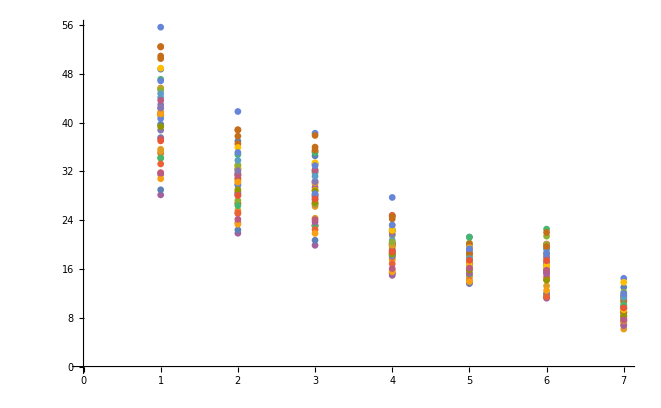

```mathematica
ListPlot[ListOfEnergiesResultsNeutrons]
```

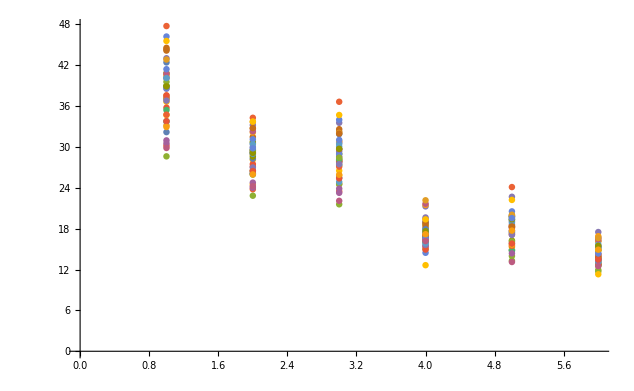

```mathematica
ListPlot[ListOfEnergiesResultsProtons]
```

```mathematica
NumberBasis=2;
```

```mathematica
(*We are multiplying by the norm of the first case to set a scale so that when computing the SVD coefficients the seed (1,0,0,...) makes sense. This means that an already good approximation to any solution is a "1" on the first mode, and zeroes on the other.*)
```

```mathematica
BasisNeutronsGSVD=Table[(Transpose[SingularValueDecomposition[Transpose[BasisNeutronsG][[j]]][[3]]][[1;;NumberBasis]])*Norm[BasisNeutronsG[[1]][[j]]],{j,1,Length[Transpose[BasisNeutronsG]]}];
BasisProtonsGSVD=Table[(Transpose[SingularValueDecomposition[Transpose[BasisProtonsG][[j]]][[3]]][[1;;NumberBasis]])*Norm[BasisProtonsG[[1]][[j]]],{j,1,Length[Transpose[BasisProtonsG]]}];
```

```mathematica
(*The following part is just annoying: We need to flip some of the SVD decomposition first component such that they are aligned with the regular solutions (meaning that the seed [1,0] for the coefficients of two basis for example makes sense, otherwise the seed should be [-1.0] for some cases)*)
```

```mathematica
BasisNeutronsGSVD[[1]][[1]]=-BasisNeutronsGSVD[[1]][[1]];
BasisNeutronsGSVD[[2]][[1]]=-BasisNeutronsGSVD[[2]][[1]];
BasisNeutronsGSVD[[3]][[1]]=-BasisNeutronsGSVD[[3]][[1]];
BasisNeutronsGSVD[[4]][[1]]=-BasisNeutronsGSVD[[4]][[1]];
(*BasisNeutronsGSVD[[5]][[1]]=-BasisNeutronsGSVD[[5]][[1]];*)
BasisNeutronsGSVD[[6]][[1]]=-BasisNeutronsGSVD[[6]][[1]];
BasisNeutronsGSVD[[7]][[1]]=-BasisNeutronsGSVD[[7]][[1]];
```

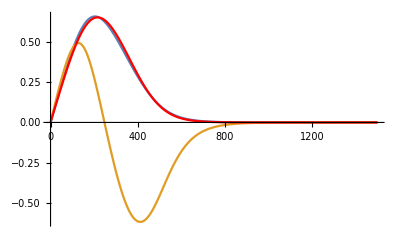
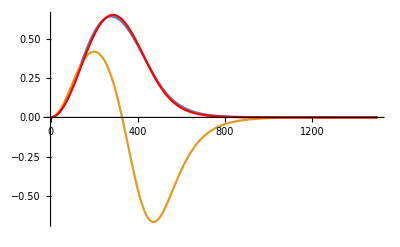
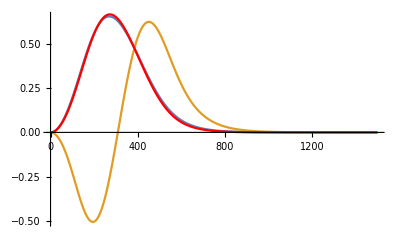
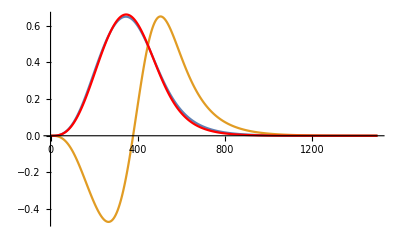
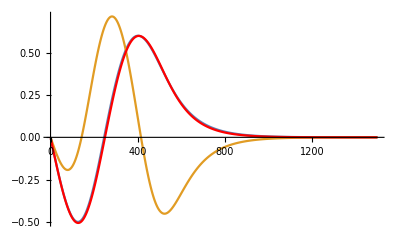
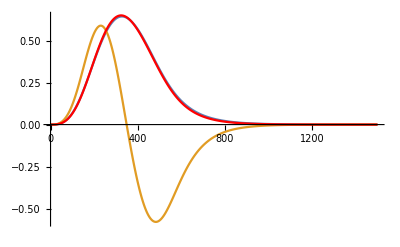
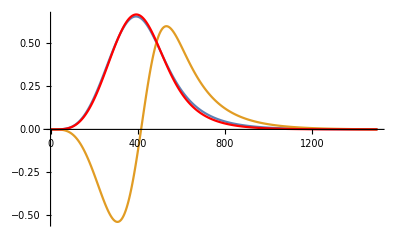

```mathematica
Table[Show[ListPlot[BasisNeutronsGSVD[[j]],Joined->True,PlotRange->All],ListPlot[BasisNeutronsG[[1]][[j]],Joined->True,PlotRange->All,PlotStyle->Red]],{j,1,Length[BasisNeutronsGSVD]}]
```

```mathematica
BasisProtonsGSVD[[1]][[1]]=-BasisProtonsGSVD[[1]][[1]];
BasisProtonsGSVD[[2]][[1]]=-BasisProtonsGSVD[[2]][[1]];
BasisProtonsGSVD[[3]][[1]]=-BasisProtonsGSVD[[3]][[1]];
BasisProtonsGSVD[[4]][[1]]=-BasisProtonsGSVD[[4]][[1]];
BasisProtonsGSVD[[5]][[1]]=-BasisProtonsGSVD[[5]][[1]];
(*BasisProtonsGSVD[[6]][[1]]=-BasisProtonsGSVD[[6]][[1]];*)
```

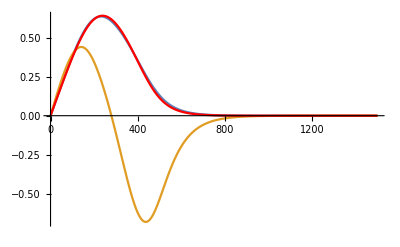
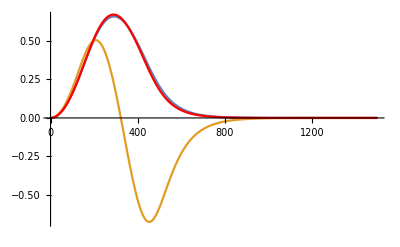
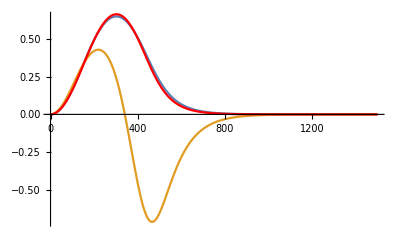
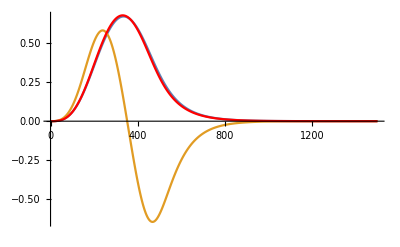
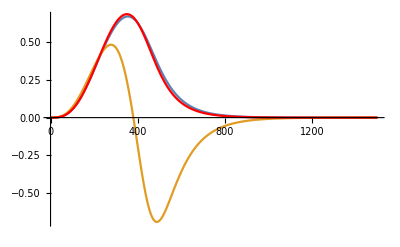
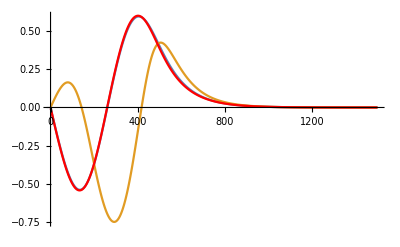

```mathematica
Table[Show[ListPlot[BasisProtonsGSVD[[j]],Joined->True,PlotRange->All],ListPlot[BasisProtonsG[[1]][[j]],Joined->True,PlotRange->All,PlotStyle->Red]],{j,1,Length[BasisProtonsGSVD]}]
```

```mathematica
Solutions0ForRB=IterativeSolver[ApplyingRulesParameters[NMConstantsToParameters[NMConstants0]],GuessToTry,{ProtonLevelsKappa,NeutronLevelsKappa}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
Solutions0ForRB[[2]]
```

{{37.732,29.8913,29.0881,19.7424,19.1963,16.0311},{36.7188,27.375,25.7535,17.7096,15.5362,14.3899,8.08703}}

```mathematica
ListOfEnergies
```

{{37.75,29.91,29.11,19.76,19.21,16.05},{36.719,27.375,25.75,17.71,15.53,14.38,8.09}}

```mathematica
(Solutions0ForRB[[2]][[1]]-ListOfEnergies[[1]])*1000
```

{-18.0077,-18.685,-21.8957,-17.6329,-13.7445,-18.882}

```mathematica
(Solutions0ForRB[[2]][[2]]-ListOfEnergies[[2]])*1000
```

{-0.210831,-0.00474313,3.46368,-0.35811,6.23584,9.8561,-2.97186}

```mathematica
NeutronsGCoeffs=Array[NeutronsGCoeffs0,{Length[BasisNeutronsGSVD],NumberBasis}];
ProtonsGCoeffs=Array[ProtonsGCoeffs0,{Length[BasisProtonsGSVD],NumberBasis}];
```

```mathematica
NeutronsGTrialFuncs=Table[Transpose[BasisNeutronsGSVD[[j]]].NeutronsGCoeffs[[j]],{j,1,Length[BasisNeutronsGSVD]}];
ProtonsGTrialFuncs=Table[Transpose[BasisProtonsGSVD[[j]]].ProtonsGCoeffs[[j]],{j,1,Length[BasisProtonsGSVD]}];
```

```mathematica
(*Example on how to convert these functions to *)
```

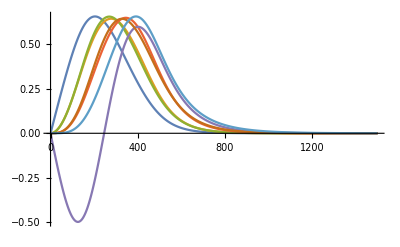

```mathematica
ListPlot[NeutronsGTrialFuncs/.Thread[Flatten[NeutronsGCoeffs]->Flatten[ConstantArray[Join[{1},ConstantArray[0,NumberBasis-1]],Length[NeutronsGCoeffs]]]],Joined->True,PlotRange->All]
```

```mathematica
DensitiesTrial=DensitiesAndFieldsBuilder[{ProtonsGTrialFuncs,NeutronsGTrialFuncs},ListOfChis];
```

```mathematica
ProtonsGEquationsGalerAffine={};
NeutronsGEquationsGalerAffine={};
```

```mathematica
ProtonsGEquationsGalerNONAffine={};
NeutronsGEquationsGalerNONAffine={};
```

```mathematica
(*ProtonsGEquationsGalerV1={};
NeutronsGEquationsGalerV1={};*)
```

```mathematica
ProtonsNormEqs={};
NeutronsNormEqs={};
```

```mathematica
EnergiesProtons=Array[EP,Length[ListOfChis[[1]]]]
EnergiesNeutrons=Array[EN,Length[ListOfChis[[2]]]]
```

{EP[1],EP[2],EP[3],EP[4],EP[5],EP[6]}

{EN[1],EN[2],EN[3],EN[4],EN[5],EN[6],EN[7]}

```mathematica
(*Proton cycle*)
```

```mathematica
ApplyingRulesParameters[Params0]
```

{t0→-2078.33,x0→0.0536509,t1→239.401,x1→-5.07706,t2→1575.29,x2→-1.36649,t3→14263.6,x3→-0.162747,W→142.633,sig→0.270018}

```mathematica
VariablesGaler
```

{ProtonsGCoeffs0[1,1],ProtonsGCoeffs0[1,2],ProtonsGCoeffs0[2,1],ProtonsGCoeffs0[2,2],ProtonsGCoeffs0[3,1],ProtonsGCoeffs0[3,2],ProtonsGCoeffs0[4,1],ProtonsGCoeffs0[4,2],ProtonsGCoeffs0[5,1],ProtonsGCoeffs0[5,2],ProtonsGCoeffs0[6,1],ProtonsGCoeffs0[6,2],NeutronsGCoeffs0[1,1],NeutronsGCoeffs0[1,2],NeutronsGCoeffs0[2,1],NeutronsGCoeffs0[2,2],NeutronsGCoeffs0[3,1],NeutronsGCoeffs0[3,2],NeutronsGCoeffs0[4,1],NeutronsGCoeffs0[4,2],NeutronsGCoeffs0[5,1],NeutronsGCoeffs0[5,2],NeutronsGCoeffs0[6,1],NeutronsGCoeffs0[6,2],NeutronsGCoeffs0[7,1],NeutronsGCoeffs0[7,2],EP[1],EP[2],EP[3],EP[4],EP[5],EP[6],EN[1],EN[2],EN[3],EN[4],EN[5],EN[6],EN[7]}

```mathematica
coeff0={1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0}
```

{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0}

```mathematica
DensitiesBuilderRhoPAndRhoN[ListOfWaveFuncs_,ChiValueList_]:=Module[{rhonIN,rhopIN,protfuncsIN,neutfuncsIN},

rhopIN=ConstantArray[0,Length[x]];
rhonIN=ConstantArray[0,Length[x]];

protfuncsIN=ListOfWaveFuncs[[1]];
neutfuncsIN=ListOfWaveFuncs[[2]];

(*Proton loop*)
For[ij=1,ij<=Length[protfuncsIN],ij++,
g2=protfuncsIN[[ij]]^2;

rhopIN=rhopIN+g2*(2*(Abs[ChiValueList[[1]][[ij]]]-1/2)+1);

];
rhopIN=rhopIN/(4*Pi)*(1/x^2);

(*rhop[[1]]=rhop[[2]];*)
(****************************)
(*Neutron loop*)

For[ij=1,ij<=Length[neutfuncsIN],ij++,
g2=neutfuncsIN[[ij]]^2;

rhonIN=rhonIN+g2*(2*(Abs[ChiValueList[[2]][[ij]]]-1/2)+1);

];
rhonIN=rhonIN/(4*Pi)*(1/x^2);

(*rhon[[1]]=rhon[[2]];*)
(****************************)




(*Returns {rhop,rhon}*)
{  rhopIN,rhonIN}


]
```

```mathematica
(*These two functions are built in such a way that they don't get evaluated until a numerical argument is passed to them. This is important so that the final equations can be passed to Fortran with that nonAffine part untoched, to be evaluated there.*)
```

```mathematica
FProtons[Coeffs_?(VectorQ[#1,NumericQ]&),paramsF_,ProtonIndex_]:=Module[{RHOPIN,RHONIN,DENSIN,WFIN,WFListIn,EqsIntermediateIN},
GlobalVariableP=GlobalVariableP+1;


WFListIn={
ProtonsGTrialFuncs/.Table[VariablesGaler[[iIN]]->Coeffs[[iIN]],{iIN,1,2*(Length[NeutronsGCoeffs]+Length[ProtonsGCoeffs])}]

,
NeutronsGTrialFuncs/.Table[VariablesGaler[[iIN]]->Coeffs[[iIN]],{iIN,1,2*(Length[NeutronsGCoeffs]+Length[ProtonsGCoeffs])}]
};

DENSIN=DensitiesBuilderRhoPAndRhoN[WFListIn,ListOfChis];
EqsIntermediateIN=eqnsPRBNONAffine/.ApplyingRulesParameters[paramsF];
EqsIntermediateIN/.{rhop->DENSIN[[1]],rhon->DENSIN[[2]],rho->DENSIN[[1]],rhotot->(DENSIN[[1]]+DENSIN[[2]]),WF->WFListIn[[1]][[ProtonIndex]],e->e0}

]
```

```mathematica
GlobalVariableP=0;
```

```mathematica
GlobalVariableN=0;
```

```mathematica
FNeutrons[Coeffs_?(VectorQ[#1,NumericQ]&),paramsF_,NeutronIndex_]:=Module[{RHOPIN,RHONIN,DENSIN,EqsIntermediateIN,WFListIn},
GlobalVariableN=GlobalVariableN+1;
WFListIn={
ProtonsGTrialFuncs/.Table[VariablesGaler[[iIN]]->Coeffs[[iIN]],{iIN,1,2*(Length[NeutronsGCoeffs]+Length[ProtonsGCoeffs])}]

,
NeutronsGTrialFuncs/.Table[VariablesGaler[[iIN]]->Coeffs[[iIN]],{iIN,1,2*(Length[NeutronsGCoeffs]+Length[ProtonsGCoeffs])}]
};

DENSIN=DensitiesBuilderRhoPAndRhoN[WFListIn,ListOfChis];


EqsIntermediateIN=eqnsNRBNONAffine/.ApplyingRulesParameters[paramsF];
EqsIntermediateIN/.{rhop->DENSIN[[1]],rhon->DENSIN[[2]],rho->DENSIN[[2]],rhotot->(DENSIN[[1]]+DENSIN[[2]]),WF->WFListIn[[2]][[NeutronIndex]],e->0}
]
```

```mathematica
varPols=Flatten[{ProtonsGCoeffs,NeutronsGCoeffs}]
```

{ProtonsGCoeffs0[1,1],ProtonsGCoeffs0[1,2],ProtonsGCoeffs0[2,1],ProtonsGCoeffs0[2,2],ProtonsGCoeffs0[3,1],ProtonsGCoeffs0[3,2],ProtonsGCoeffs0[4,1],ProtonsGCoeffs0[4,2],ProtonsGCoeffs0[5,1],ProtonsGCoeffs0[5,2],ProtonsGCoeffs0[6,1],ProtonsGCoeffs0[6,2],NeutronsGCoeffs0[1,1],NeutronsGCoeffs0[1,2],NeutronsGCoeffs0[2,1],NeutronsGCoeffs0[2,2],NeutronsGCoeffs0[3,1],NeutronsGCoeffs0[3,2],NeutronsGCoeffs0[4,1],NeutronsGCoeffs0[4,2],NeutronsGCoeffs0[5,1],NeutronsGCoeffs0[5,2],NeutronsGCoeffs0[6,1],NeutronsGCoeffs0[6,2],NeutronsGCoeffs0[7,1],NeutronsGCoeffs0[7,2]}

```mathematica
paramsHold={t0,x0,t1,x1,t2,x2,t3,x3,W,sig};
```

```mathematica
(*Proton cycle*)
```

```mathematica
For[i=1,i<=Length[ListOfChis[[1]]],i++,

ChiValue=ListOfChis[[1]][[i]];
If[ChiValue >= 0,
L0=ChiValue,
L0=-1-ChiValue
];

J0=Abs[ChiValue]-1/2;

If[Mod[L0,2]==0,

(*Affine Part*)
AppendTo[ProtonsGEquationsGalerAffine,eqnsPRBAffine/.{
J->J0,L->L0,
rhop->DensitiesTrial[[1]],rhon->DensitiesTrial[[2]],rhotot->DensitiesTrial[[3]],taup->DensitiesTrial[[4]],taun->DensitiesTrial[[5]],tautot->DensitiesTrial[[6]],jscp->DensitiesTrial[[7]],jscn->DensitiesTrial[[8]],jsctot->DensitiesTrial[[9]],AField->DensitiesTrial[[10]],
rho->DensitiesTrial[[1]],tau->DensitiesTrial[[4]],jsc->DensitiesTrial[[7]],


(*rhopSquared->RHOPSQUARED, rhonSquared->RHONSQUARED,*)

lambda->EnergiesProtons[[i]],

(*t0->-2078.328023255641,x0->0.053650874123175374,t1->239.40081204152204,x1->-5.077055078290872,t2->1575.2893283875067,x2->-1.3664930568343383,t3->14263.6462470776,x3->-0.16274731419837107,W->142.6330444591668,sig->0.27001801150270754,*)

D1->D1MatOdd,D2->D2MatOdd,Dd1->D1MatFieldsEven,Dd2->D2MatFieldsEven,Ddd1->D1MatOdd,r->x,WF->ProtonsGTrialFuncs[[i]],e->e0

}];
(*NONAffine part*)
AppendTo[ProtonsGEquationsGalerNONAffine,


eqnsPRBNONAffine/.{
J->J0,L->L0,
rhop->DensitiesTrial[[1]],rhon->DensitiesTrial[[2]],rhotot->DensitiesTrial[[3]],taup->DensitiesTrial[[4]],taun->DensitiesTrial[[5]],tautot->DensitiesTrial[[6]],jscp->DensitiesTrial[[7]],jscn->DensitiesTrial[[8]],jsctot->DensitiesTrial[[9]],AField->DensitiesTrial[[10]],
rho->DensitiesTrial[[1]],tau->DensitiesTrial[[4]],jsc->DensitiesTrial[[7]],



lambda->EnergiesProtons[[i]],



D1->D1MatOdd,D2->D2MatOdd,Dd1->D1MatFieldsEven,Dd2->D2MatFieldsEven,Ddd1->D1MatOdd,r->x,WF->ProtonsGTrialFuncs[[i]],e->e0

}];



AppendTo[ProtonsNormEqs,(ProtonsGTrialFuncs[[i]].ProtonsGTrialFuncs[[i]])*dx-1],

(*Affine Part*)
AppendTo[ProtonsGEquationsGalerAffine,eqnsPRBAffine/.{
J->J0,L->L0,

rhop->DensitiesTrial[[1]],rhon->DensitiesTrial[[2]],rhotot->DensitiesTrial[[3]],taup->DensitiesTrial[[4]],taun->DensitiesTrial[[5]],tautot->DensitiesTrial[[6]],jscp->DensitiesTrial[[7]],jscn->DensitiesTrial[[8]],jsctot->DensitiesTrial[[9]],AField->DensitiesTrial[[10]],
rho->DensitiesTrial[[1]],tau->DensitiesTrial[[4]],jsc->DensitiesTrial[[7]],



lambda->EnergiesProtons[[i]],


D1->D1MatEven,D2->D2MatEven,Dd1->D1MatFieldsEven,Dd2->D2MatFieldsEven,Ddd1->D1MatOdd,r->x,WF->ProtonsGTrialFuncs[[i]],e->e0

}];

(*NONAffine Part*)
AppendTo[ProtonsGEquationsGalerNONAffine,eqnsPRBNONAffine/.{
J->J0,L->L0,

rhop->DensitiesTrial[[1]],rhon->DensitiesTrial[[2]],rhotot->DensitiesTrial[[3]],taup->DensitiesTrial[[4]],taun->DensitiesTrial[[5]],tautot->DensitiesTrial[[6]],jscp->DensitiesTrial[[7]],jscn->DensitiesTrial[[8]],jsctot->DensitiesTrial[[9]],AField->DensitiesTrial[[10]],
rho->DensitiesTrial[[1]],tau->DensitiesTrial[[4]],jsc->DensitiesTrial[[7]],



lambda->EnergiesProtons[[i]],

D1->D1MatEven,D2->D2MatEven,Dd1->D1MatFieldsEven,Dd2->D2MatFieldsEven,Ddd1->D1MatOdd,r->x,WF->ProtonsGTrialFuncs[[i]],e->e0

}];


AppendTo[ProtonsNormEqs,(ProtonsGTrialFuncs[[i]].ProtonsGTrialFuncs[[i]])*dx-1]

]



]
```

```mathematica
Length[CoefficientRules[ProtonsGEquationsGalerAffine[[1]][[1]],varPols]]
```

78

```mathematica
(*Neutron cycle*)

For[i=1,i<=Length[ListOfChis[[2]]],i++,
ChiValue=ListOfChis[[2]][[i]];
If[ChiValue >= 0,
L0=ChiValue,
L0=-1-ChiValue
];

J0=Abs[ChiValue]-1/2;

If[Mod[L0,2]==0,
(*Affine part*)
AppendTo[NeutronsGEquationsGalerAffine,eqnsNRBAffine/.{
J->J0,L->L0,
rhop->DensitiesTrial[[1]],rhon->DensitiesTrial[[2]],rhotot->DensitiesTrial[[3]],taup->DensitiesTrial[[4]],taun->DensitiesTrial[[5]],tautot->DensitiesTrial[[6]],jscp->DensitiesTrial[[7]],jscn->DensitiesTrial[[8]],jsctot->DensitiesTrial[[9]],AField->DensitiesTrial[[10]],
rho->DensitiesTrial[[2]],tau->DensitiesTrial[[5]],jsc->DensitiesTrial[[8]],



lambda->EnergiesNeutrons[[i]],
D1->D1MatOdd,D2->D2MatOdd,Dd1->D1MatFieldsEven,Dd2->D2MatFieldsEven,Ddd1->D1MatOdd,r->x,WF->NeutronsGTrialFuncs[[i]],e->0

}];
(*NONAffine part*)
AppendTo[NeutronsGEquationsGalerNONAffine,eqnsNRBNONAffine/.{
J->J0,L->L0,
rhop->DensitiesTrial[[1]],rhon->DensitiesTrial[[2]],rhotot->DensitiesTrial[[3]],taup->DensitiesTrial[[4]],taun->DensitiesTrial[[5]],tautot->DensitiesTrial[[6]],jscp->DensitiesTrial[[7]],jscn->DensitiesTrial[[8]],jsctot->DensitiesTrial[[9]],AField->DensitiesTrial[[10]],
rho->DensitiesTrial[[2]],tau->DensitiesTrial[[5]],jsc->DensitiesTrial[[8]],


lambda->EnergiesNeutrons[[i]],
D1->D1MatOdd,D2->D2MatOdd,Dd1->D1MatFieldsEven,Dd2->D2MatFieldsEven,Ddd1->D1MatOdd,r->x,WF->NeutronsGTrialFuncs[[i]],e->0

}];



AppendTo[NeutronsNormEqs,(NeutronsGTrialFuncs[[i]].NeutronsGTrialFuncs[[i]])*dx-1],
(*Affine part*)
AppendTo[NeutronsGEquationsGalerAffine,eqnsNRBAffine/.{
J->J0,L->L0,

rhop->DensitiesTrial[[1]],rhon->DensitiesTrial[[2]],rhotot->DensitiesTrial[[3]],taup->DensitiesTrial[[4]],taun->DensitiesTrial[[5]],tautot->DensitiesTrial[[6]],jscp->DensitiesTrial[[7]],jscn->DensitiesTrial[[8]],jsctot->DensitiesTrial[[9]],AField->DensitiesTrial[[10]],
rho->DensitiesTrial[[2]],tau->DensitiesTrial[[5]],jsc->DensitiesTrial[[8]],


lambda->EnergiesNeutrons[[i]],




D1->D1MatEven,D2->D2MatEven,Dd1->D1MatFieldsEven,Dd2->D2MatFieldsEven,Ddd1->D1MatOdd,r->x,WF->NeutronsGTrialFuncs[[i]],e->0

}];

(*NONAffine part*)
AppendTo[NeutronsGEquationsGalerNONAffine,eqnsNRBNONAffine/.{
J->J0,L->L0,

rhop->DensitiesTrial[[1]],rhon->DensitiesTrial[[2]],rhotot->DensitiesTrial[[3]],taup->DensitiesTrial[[4]],taun->DensitiesTrial[[5]],tautot->DensitiesTrial[[6]],jscp->DensitiesTrial[[7]],jscn->DensitiesTrial[[8]],jsctot->DensitiesTrial[[9]],AField->DensitiesTrial[[10]],
rho->DensitiesTrial[[2]],tau->DensitiesTrial[[5]],jsc->DensitiesTrial[[8]],


lambda->EnergiesNeutrons[[i]],



D1->D1MatEven,D2->D2MatEven,Dd1->D1MatFieldsEven,Dd2->D2MatFieldsEven,Ddd1->D1MatOdd,r->x,WF->NeutronsGTrialFuncs[[i]],e->0

}];


AppendTo[NeutronsNormEqs,(NeutronsGTrialFuncs[[i]].NeutronsGTrialFuncs[[i]])*dx-1]

]



]
```

```mathematica
FinalEquationsGaler={};
```

```mathematica
FinalEquationsGalerForKyle={};
```

```mathematica
JudgesForKyleProtons={};
```

```mathematica
JudgesForKyleNeutrons={};
```

```mathematica
For[hbasis=1,hbasis<=NumberBasis,hbasis++,
For[hprotons=1,hprotons<=Length[ListOfChis[[1]]],hprotons++,
Print[hbasis,hprotons];
EqAffine=Collect[
Expand[BasisProtonsGSVD[[hprotons]][[hbasis]].ProtonsGEquationsGalerAffine[[hprotons]]],varPols];

AppendTo[FinalEquationsGaler,EqAffine+
+BasisProtonsGSVD[[hprotons]][[hbasis]].FProtons[varPols,paramsHold,hprotons]
==0];




AppendTo[FinalEquationsGalerForKyle,EqAffine+PsiProtons[hprotons,hbasis].FNonAffineProtons[Coefficients,Parameters,hprotons]
];

AppendTo[JudgesForKyleProtons,BasisProtonsGSVD[[hprotons]][[hbasis]]];


]

];
```

11

12

13

14

15

16

21

22

23

24

25

26

```mathematica
For[hbasis=1,hbasis<=NumberBasis,hbasis++,
For[hneutrons=1,hneutrons<=Length[ListOfChis[[2]]],hneutrons++,
Print[hbasis,hneutrons];



EqAffine=Collect[Expand[BasisNeutronsGSVD[[hneutrons]][[hbasis]].NeutronsGEquationsGalerAffine[[hneutrons]]],varPols];

AppendTo[FinalEquationsGaler,EqAffine+
+BasisNeutronsGSVD[[hneutrons]][[hbasis]].FNeutrons[varPols,paramsHold,hneutrons]
==0];


AppendTo[FinalEquationsGalerForKyle,EqAffine+
+PsiNeutrons[hneutrons,hbasis].FNonAffineNeutrons[Coefficients,Parameters,hneutrons]
==0];

AppendTo[JudgesForKyleNeutrons,BasisNeutronsGSVD[[hneutrons]][[hbasis]]]





]
];
```

11

12

13

14

15

16

17

21

22

23

24

25

26

27

```mathematica
For[i=1,i<=Length[ProtonsNormEqs],i++,
AppendTo[FinalEquationsGaler,Expand[ProtonsNormEqs[[i]]]==0];
AppendTo[FinalEquationsGalerForKyle,Expand[ProtonsNormEqs[[i]]]==0];
]
```

```mathematica
For[i=1,i<=Length[NeutronsNormEqs],i++,
AppendTo[FinalEquationsGaler,Expand[NeutronsNormEqs[[i]]]==0];
AppendTo[FinalEquationsGalerForKyle,Expand[NeutronsNormEqs[[i]]]==0];
]
```

```mathematica
Length[FinalEquationsGaler]
```

39

```mathematica
VariablesGaler=Flatten[Join[ProtonsGCoeffs,NeutronsGCoeffs,EnergiesProtons,EnergiesNeutrons]]
```

{ProtonsGCoeffs0[1,1],ProtonsGCoeffs0[1,2],ProtonsGCoeffs0[2,1],ProtonsGCoeffs0[2,2],ProtonsGCoeffs0[3,1],ProtonsGCoeffs0[3,2],ProtonsGCoeffs0[4,1],ProtonsGCoeffs0[4,2],ProtonsGCoeffs0[5,1],ProtonsGCoeffs0[5,2],ProtonsGCoeffs0[6,1],ProtonsGCoeffs0[6,2],NeutronsGCoeffs0[1,1],NeutronsGCoeffs0[1,2],NeutronsGCoeffs0[2,1],NeutronsGCoeffs0[2,2],NeutronsGCoeffs0[3,1],NeutronsGCoeffs0[3,2],NeutronsGCoeffs0[4,1],NeutronsGCoeffs0[4,2],NeutronsGCoeffs0[5,1],NeutronsGCoeffs0[5,2],NeutronsGCoeffs0[6,1],NeutronsGCoeffs0[6,2],NeutronsGCoeffs0[7,1],NeutronsGCoeffs0[7,2],EP[1],EP[2],EP[3],EP[4],EP[5],EP[6],EN[1],EN[2],EN[3],EN[4],EN[5],EN[6],EN[7]}

```mathematica
Length[VariablesGaler]
```

39

```mathematica
GuessGaler=Flatten[Join[

Flatten[ConstantArray[Join[{1},ConstantArray[0,NumberBasis-1]],Length[NeutronsGCoeffs]]],
Flatten[ConstantArray[Join[{1},ConstantArray[0,NumberBasis-1]],Length[ProtonsGCoeffs]]],
ListOfEnergies[[1]],ListOfEnergies[[2]]

]
]
```

```mathematica
Timing[FinalEqs=FinalEquationsGaler/.ApplyingRulesParameters[Params0];]
```

{0.015625,Null}

```mathematica
(*This timing looks awful, but it is because Mathematica is not very fast solving these equations. The real speed up comes when compiling the equations and solving them in another speed-focused language*)
```

```mathematica
AbsoluteTiming[SolGaler=FindRoot[FinalEqs,Transpose[{VariablesGaler,GuessGaler}],PrecisionGoal->20,MaxIterations->300]]
```

{99.8037,{ProtonsGCoeffs0[1,1]→0.999639,ProtonsGCoeffs0[1,2]→-0.0268575,ProtonsGCoeffs0[2,1]→0.999913,ProtonsGCoeffs0[2,2]→-0.0131807,ProtonsGCoeffs0[3,1]→0.999865,ProtonsGCoeffs0[3,2]→-0.0164033,ProtonsGCoeffs0[4,1]→0.999998,ProtonsGCoeffs0[4,2]→0.00193474,ProtonsGCoeffs0[5,1]→0.999936,ProtonsGCoeffs0[5,2]→-0.0113038,ProtonsGCoeffs0[6,1]→0.999979,ProtonsGCoeffs0[6,2]→-0.00651295,NeutronsGCoeffs0[1,1]→0.999863,NeutronsGCoeffs0[1,2]→0.0165688,NeutronsGCoeffs0[2,1]→0.999962,NeutronsGCoeffs0[2,2]→0.00876434,NeutronsGCoeffs0[3,1]→0.99995,NeutronsGCoeffs0[3,2]→-0.0099623,NeutronsGCoeffs0[4,1]→0.999972,NeutronsGCoeffs0[4,2]→-0.00744299,NeutronsGCoeffs0[5,1]→0.999944,NeutronsGCoeffs0[5,2]→0.0105573,NeutronsGCoeffs0[6,1]→0.999919,NeutronsGCoeffs0[6,2]→0.0127319,NeutronsGCoeffs0[7,1]→0.999868,NeutronsGCoeffs0[7,2]→-0.016252,EP[1]→37.6511,EP[2]→29.8752,EP[3]→29.1739,EP[4]→19.7879,EP[5]→19.2984,EP[6]→15.8622,EN[1]→36.8315,EN[2]→27.3567,EN[3]→25.7356,EN[4]→17.6108,EN[5]→15.5667,EN[6]→14.341,EN[7]→7.99852}}

```mathematica
Solutions0ForRB[[2]]
```

{{37.732,29.8913,29.0881,19.7424,19.1963,16.0311},{36.7188,27.375,25.7535,17.7096,15.5362,14.3899,8.08703}}

```mathematica
Length[CoefficientRules[FinalEquationsGaler[[1]][[1]],varPols]]
```

79

```mathematica
(*In here we export the polynomial equations in the coefficients and parameters (the affine part) plus the non affine part treated as a black box function that will be computed in Fortran.*)
```

```mathematica
Export["KylePolynomialsFullyTrained"<>ToString[NumberBasis]<>".txt",{FinalEquationsGalerForKyle}]
```

KylePolynomialsFullyTrained2.txt

```mathematica
Export["KyleJudgesProtonsFullyTrained"<>ToString[NumberBasis]<>".txt",JudgesForKyleProtons]
```

KyleJudgesProtonsFullyTrained2.txt

```mathematica
Export["KyleJudgesNeutronsFullyTrained"<>ToString[NumberBasis]<>".txt",JudgesForKyleNeutrons]
```

KyleJudgesNeutronsFullyTrained2.txt